```mathematica
2-2
```

0

# Penrose's dodecahedral no-go theorem

Nicholas Wheeler
Reed College Physics Department
1 April 2008

### Short history of no-go theorems

"No-go theorems" come in a wide variety of flavors, but all have this in common: they proceed from othodox quantum mechanics to propositions that preclude explanation by appeal to hidden variable theories of a certain type (specifically: "non-contextual" hidden variable theories, theories that embody the "local realism" contemplated by EPR). John Bell had argued already in "On the Einstein-Podolsky-Rosen paradox" (Physics 1, 195-200 (1964), reprinted as paper #2 in Speakable & Unspeakable in Quantum Mechanics (1987)) that such theories lead to a statistical inequality which Alice and Bob, if equipped with proper instruments, would be able to demonstrate is violated if orthodox quantum mechanics is correct. "Is orthodox quantum mechanics correct?" became at this point a question that could be addressed experimentally—and was: for an account of this work see Amir D. Aczel, Entanglement (2001) and Alain Aspect's contribution "Testing Bell's inequalities" to J. Ellis & D. Amati (eds.) Quantum Reflections (2000). 

In §5 of "On the problem of hidden variables in quantum theory" (Rev. Mod. Phys. 38, 447-452 (1966),  reprinted as paper #1 in Speakable & Unspeakable) Bell draws attention to the direct relevance of some consequences—which he develops in a couple of pages—of a theorem developed by A. M. Gleason ("Measures on the closed subspaces of a Hilbert space," Journal of Mathematics & Mechanics 6, 885-893(1957)), to which his own attention had been directed by J. M. Jauch (who was by then at the University of Geneva). In §7.6 of his The Philosophy of Quantum Mechanics: The Interpretations of Quantum Mechanics in Historical Perspective (1974) Max Jammer reports that Gleason took his motivation from George Mackey's effort to place quantum mechanics on mathematically secure foundations.  

On his page 322, Jammer describes the entrance of Simon B. Kochen & Ernst P. Specker ("The problem of hidden variables in quantum mechanics," Journal of Mathematics & Mechanics 17, 59-87 (1967)) as actors in this story, and on pages 324-326 he presents "what is probably the simplest version of the K-S argument." K-S arguments, in whatever specific form, invariably lead from orthodox quantum mechanics to a geometrical condition which no non-contextual hidden variable theory can satisfy, and are typically quite intricate. In their own first version of the argument (Jammer, page 328) they employed "a set of 117 different coordinate decompositions of the spin angular momentum of orthohelium in its lowest orbital state." That number was reduced to 33 by Asher Peres ("Two simple proofs of the Kochen-Specker theorem," J. Phys. A: Math. Gen. 24 (1990a) L175) and soon thereafter to 24 by Peres ("Incompatible results of quantum measurements," Phys. Lett. A (1990b) 107-108) and by N. D. Mermin ("Simple unified form for the major no-hidden-variables theorems," Phys. Rev. Lett. 65, 3373 (1990)), both of whom, however, worked in 4-space rather than 3-space. The 24-ray construction was recognized by Peres (see Exercise 7.12 on page 201 in Peres' Quantum Theory: Concepts & Methods (1993)) to be very closely related to convex regular 4-polytope known as the "24-cell."

```mathematica
Hyperlink["24-cell","http://en.wikipedia.org/wiki/24-cell" ]
```

```mathematica
Hyperlink["Escher's Waterfall", "http://en.wikipedia.org/wiki/Waterfall_(M._C._Escher)"]
```

```mathematica
Import["/Volumes/NONLINEAR/Simulated QM/No-go Theorems/Waterfall2.rtfd/300px-Escher_Waterfall.jpg"]
```

-Graphics-

### Penrose's dodecahedral no-go theorem

By 1993, Penrose had worked out the details of his dodecahedral no-go theorem (J. Zimba & R. Penrose, "On Bell non-locality without probabilities: more curious geometry" Stud. Hist. Phil. Sci. 24, 697-720 (1993)). Penrose gave a popular account of his dodecahedral work—presented as a game—in §5.3 "Magic dodecahedra" of Shadows of the Mind (1994) pages 240-246 and a more technical account in §5.18 "The magic dodecahedra explained," pages 296-300, and Appendix B, "The non-colorability of the dodecahedron," pages 300-301. He provides another technical discussion—this time without Zimba's assistance—in "On Bell non-locality without probabilities: some curious geometry," which is the leading essay in J. Ellis & D. Amati (eds.) Quantum Reflections (2000). 

In early 2007 I produced seven long Mathematica notebooks that treat various aspects of Penrose's argument and several more that treat closely related subjects. At that time I relied heavily on J. E. Massad & P. K. Aravind, "The Penrose dodecahedron revisited," AJP 67, 631-638 (1999)—the paper upon which Tom Wieting based the physics seminar where I first learn of Penrose's dodecahedral work, which at the time I found to be more picturesque than convincingly informative.

My objective here will be—by leaving out much of the repetitive detail—to construct a briefer and more focused account of the essential drift of Penrose's argument. But I will not attempt to match the sharply focused brevity of the account given on Peres' page 212 (upon which I do draw heavily in first sections of this essay). 

Penrose recognized that the arguments that led to the theorems devised by Peres and Mermin acquired their elegant brevity partly from the fact that they worked in 4-dimensions (rather than 3-dimensions, as Kochen-Specker had done).  But he held it to be a defect of those arguments that they employ operators of a form

```mathematica
𝕒⊗𝕓
```

that represent the action of meters of a type available only to God, not to Alice and Bob, who are stuck with instruments of the types

```mathematica
𝕒⊗𝕀
𝕀⊗𝕓
```

That is a defect he managed to remove.

Mention of n-dimensional Hilbert space brings naturally to mind (see my "Spin matrices for arbitrary spin" (2000)) the quantum theory of spin/angular momentum s=(n-1)/2, which in the case n = 4 means spin 3/2. Which, I take it, is the reason—one of the reasons—that Penrose looks to spin 3/2rather than the spin 1/2 and 2/2 that had figured in earlier treatments of this subject.

### Basic theory of spin 3/2

REMARK: I will, for a while, be borrowing material from the notebook "Penrose Dodecahedron: Part I," but will write in a way intented to illuminate the remarks (mentioned above) that Peres sets down on his page 212, and to which I have in the past not paid much attention.

On page 17 of the notes just mentioned we encounter the constructions

```mathematica
Subscript[J, 1]=ℏ/2({{0, √3, 0, 0}, {√3, 0, 2, 0}, {0, 2, 0, √3}, {0, 0, √3, 0}});
Subscript[J, 2]=ⅈ ℏ/2({{0, -√3, 0, 0}, {√3, 0, -2, 0}, {0, 2, 0, -√3}, {0, 0, √3, 0}});
Subscript[J, 3]=ℏ/2({{3, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -3}});
JJ=Subscript[J, 1].Subscript[J, 1]+Subscript[J, 2].Subscript[J, 2]+Subscript[J, 3].Subscript[J, 3];
```

Further progress requires that we assemble some machinery:

```mathematica
Comm[A_,B_]:=A.B-B.A
CompConj[A_] := A /.Complex[0,n_]->-Complex[0,n]
P_⊗Q_:=Flatten[Table[Flatten[Table[Part[Outer[Times,P,Q],i,j,k],{j,Dimensions[P]⟦2⟧}]],{i,Dimensions[P]⟦1⟧},{k,Dimensions[Q]⟦1⟧}],1]
Subscript[𝕀, 4]=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
Subscript[𝕆, 4]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

We have

```mathematica
Comm[Subscript[J, 1],Subscript[J, 2]]==ⅈ ℏ Subscript[J, 3]
Comm[Subscript[J, 2],Subscript[J, 3]]==ⅈ ℏ Subscript[J, 1]
Comm[Subscript[J, 3],Subscript[J, 1]]==ⅈ ℏ Subscript[J, 2]

Comm[JJ,Subscript[J, 1]]==Subscript[𝕆, 4]
Comm[JJ,Subscript[J, 2]]==Subscript[𝕆, 4]
Comm[JJ,Subscript[J, 3]]==Subscript[𝕆, 4]
```

True

True

True

«3 more identical outputs»

The following results

```mathematica
Eigenvalues[JJ]
```

{(15 ℏ^2)/4,(15 ℏ^2)/4,(15 ℏ^2)/4,(15 ℏ^2)/4}

```mathematica
Solve[ℏ^2 λ(λ+1)==(15 ℏ^2)/4,λ]
```

{{λ→-5/2},{λ→3/2}}

serve to establish that we are indeed talking about spin s=3/2. We therefore are not at all surprised by the following news:

```mathematica
Eigenvalues[Subscript[J, 1]]
Eigenvalues[Subscript[J, 2]]
Eigenvalues[Subscript[J, 3]]
```

{-3/2,3/2,-1/2,1/2}

{-3/2,3/2,-1/2,1/2}

{-3/2,3/2,-1/2,1/2}

These facts make obvious that we are positioned at the red dots in the following spin/angular momentum diagram:

-Graphics-

Measurement devices, in 4-state quantum theory, are respresented by 4 × 4 hermitian matrices, of which there exists a 16-parameter population (such matrices live in a 16-dimensional real vector space). But in spin theory our interest is restricted to a 3-parameter subset of that population—to matrices of the form

```mathematica
A=a1 Subscript[J, 1]+a2 Subscript[J, 2]+a3 Subscript[J, 3];
```

where the a-coefficients are real, and can/will without loss of generality be assumed to satisfy a1^2+a2^2+a3^2=1.

If, as becomes convenient at this point, we set

```mathematica
ℏ=1;
```

we have

```mathematica
2A//Simplify//MatrixForm
Simplify[Eigenvalues[A],Assumptions->{a1^2+a2^2+a3^2==1}]
```

(3 a3 | √3 (a1-ⅈ a2) | 0 | 0
√3 (a1+ⅈ a2) | a3 | 2 (a1-ⅈ a2) | 0
0 | 2 (a1+ⅈ a2) | -a3 | √3 (a1-ⅈ a2)
0 | 0 | √3 (a1+ⅈ a2) | -3 a3)

{-3/2,-1/2,1/2,3/2}

Penrose, for reasons that will emerge, attaches special importance to the eigenvector associated with the eigenvalue  λ=1/2, which (prior to normalization)  reads

```mathematica
f[a1_,a2_,a3_]:=√3 Transpose[{(a1+ⅈ a2)^3{-((a1-ⅈ a2) (1+a3))/(a1+ⅈ a2)^2,(-1+2 a3+3 a3^2)/(√3 (a1+ⅈ a2)^2),(1+3 a3)/(√3 (a1+ⅈ a2)),1}}]
```

as I demonstrate:

```mathematica
Simplify[ComplexExpand[A.f[a1,a2,a3]-1/2 f[a1,a2,a3]],Assumptions->{a1^2+a2^2+a3^2==1}]//MatrixForm
```

(0
0
0
0)

Looking to the normalization, from

```mathematica
Simplify[Transpose[CompConj[f[a1,a2,a3]]].f[a1,a2,a3],Assumptions->{a1^2+a2^2+a3^2==1}]⟦1⟧⟦1⟧
```

-8 (-1+a3) (1+a3)^2

we are led to construct

```mathematica
F[a1_,a2_,a3_]:=f[a1,a2,a3]/(√(-8 (-1+a3) (1+a3)^2))
```

which we demonstrate to be normalized:

```mathematica
Simplify[Transpose[CompConj[F[a1,a2,a3]]].F[a1,a2,a3],Assumptions->{a1^2+a2^2+a3^2==1}]⟦1⟧⟦1⟧
```

1

From Peres we acquire interest in the relationships between a = (a1
a2
a3) and b = (b1
b2
b3) that are forced by the requirement that F[a1, a2, a3]  and  F[b1, b2, b3]  be orthogonal. To make the problem manageable I set

(a1
a2
a3)=(1
0
0), (b1
b2
b3)=(Cos[α]
Sin[α]
0)

and construct

```mathematica
(Transpose[CompConj[F[1,0,0]]].F[Cos[α],Sin[α],0]//ComplexExpand)⟦1⟧⟦1⟧
```

Cos[α]/8+Cos[α]^2/2+(3 Cos[α]^3)/8+Sin[α]^2/4-9/8 Cos[α] Sin[α]^2+ⅈ (Sin[α]/8+1/4 Cos[α] Sin[α]+9/8 Cos[α]^2 Sin[α]-(3 Sin[α]^3)/8)

from which I extract the real and imaginary parts:

```mathematica
U=Cos[α]/8+Cos[α]^2/2+(3 Cos[α]^3)/8+Sin[α]^2/4-9/8 Cos[α] Sin[α]^2/.Sin[α]^2->1-Cos[α]^2
```

Cos[α]/8+Cos[α]^2/2+(3 Cos[α]^3)/8+1/4 (1-Cos[α]^2)-9/8 Cos[α] (1-Cos[α]^2)

```mathematica
V=Sin[α]/8+1/4 Cos[α] Sin[α]+9/8 Cos[α]^2 Sin[α]-(3 Sin[α]^3)/8;
```

The requirement that the real part of the inner product vanish resolves into three cases

```mathematica
Solve[U==0,Cos[α]]
```

{{Cos[α]→-1},{Cos[α]→1/3},{Cos[α]→1/2}}

each of which will be found to resolve into three subcases:

CASE 1:

```mathematica
V/.Cos[α]->-1
Solve[%==0, Sin[α]]
```

Sin[α]-(3 Sin[α]^3)/8

{{Sin[α]→0},{Sin[α]→-2 √(2/3)},{Sin[α]→2 √(2/3)}}

We ask whether the values of  Cos[α] and  Sin[α] that emerge from that argument conform to the requirement that the sum of their squares is unity:

```mathematica
(-1)^2+ (0)^2==1
(-1)^2+ (2 √(2/3))^2==1
```

True

False

The former is acceptable, the latter not.

CASE 2:

```mathematica
V/.Cos[α]->1/3
Solve[%==0, Sin[α]]
```

Sin[α]/3-(3 Sin[α]^3)/8

{{Sin[α]→0},{Sin[α]→-(2 √2)/3},{Sin[α]→(2 √2)/3}}

```mathematica
(1/3)^2+(0)^2==1
(1/3)^2+((2 √2)/3)^2==1
```

False

True

The latter is acceptable, the former not.

CASE 3:

```mathematica
V/.Cos[α]->1/2
Solve[%==0, Sin[α]]
```

(17 Sin[α])/32-(3 Sin[α]^3)/8

{{Sin[α]→0},{Sin[α]→-(√(17/3))/2},{Sin[α]→(√(17/3))/2}}

```mathematica
(1/2)^2+(0)^2==1
(1/2)^2+((√(17/3))/2)^2==1
```

False

False

We conclude that F[a1, a2, a3]  and  F[b1, b2, b3]  will be orthogonal if and only if either a.b = Cos[α] = -1 or 1/3, and proceed to demonstrate that orthogonality:

```mathematica
(Transpose[CompConj[F[1,0,0]]].F[-1,0,0])⟦1⟧⟦1⟧

(Transpose[CompConj[F[1,0,0]]].F[1/3,+(2 √2)/3,0]//ComplexExpand)⟦1⟧⟦1⟧
```

0

0

Here is a diagramatic representation of the relationship of the blue and red vectors to the black vector:

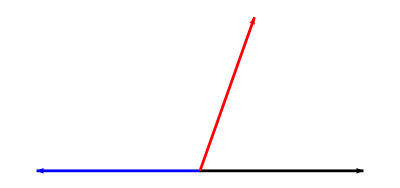

At this point, Peres would have us "recall that cos^-1(1/3) is the angle subtended at the center of a dodecahedron by a pair of next-to-adjacent vertices." I doubt that anyone—even Penrose—is in position to "recall" such a fact, though some people might be in position to "recall (or to instantly figure out) that cos^-1(1/3) is the angle subtended at the center of a cube by a pair of adjacent vertices" which is, as will emerge, an equivalent geometrical proposition. It is my impression that it was his deep understanding of the Majoriana description of general spin states (see §§ 3 and 6 of his Quantum Reflections paper) that led Penrose to think of dodecahedra in this connection.

We digress now to acquire familiarity with

### Some dodecahedral facts

Here I indent to borrow as needed from the notebook "Penrose Dodecahedron: Part II," which was written with Mathematica 5.2. Standard packages that I then had to activate by explicit command

```mathematica
Needs["PolyhedronOperations`"]
Needs["Polytopes`"]
```

provided polyhedral information that is now built into Mathematica 6.

```mathematica
Show[PolyhedronData["Dodecahedron"], Boxed->False]
```

-Graphics3D-

But Mathematica 6 presents a scrambled version of the information provided by Mathematica 5.2. So—not to waste time unscrambling things—I copy and paste from the old notebook mentioned above this list of the twenty 3-vectors that point from the origin to the twenty vertices of a dodecahedron:

```mathematica
{p11,p12,p13,p14,p15,p21,p22,p23,p24,p25,p31,p32,p33,p34,p35,p41,p42,p43,p44,p45}={{√(1/2-1/(2 √5)),1/2 (3-√5),√(1/2+1/(2 √5))},{-√(5/2-11/(2 √5)),1/2 (-1+√5),√(1/2+1/(2 √5))},{-2 √(1/5 (5-2 √5)),0,√(1/2+1/(2 √5))},{-√(5/2-11/(2 √5)),1/2 (1-√5),√(1/2+1/(2 √5))},{√(1/2-1/(2 √5)),1/2 (-3+√5),√(1/2+1/(2 √5))},{√(1/2+1/(2 √5)),1/2 (-1+√5),√(5/2-11/(2 √5))},{-√(1/5 (5-2 √5)),1,√(5/2-11/(2 √5))},{-√(2/5 (5-√5)),0,√(5/2-11/(2 √5))},{-√(1/5 (5-2 √5)),-1,√(5/2-11/(2 √5))},{√(1/2+1/(2 √5)),1/2 (1-√5),√(5/2-11/(2 √5))},{√(1/5 (5-2 √5)),1,-√(5/2-11/(2 √5))},{-√(1/2+1/(2 √5)),1/2 (-1+√5),-√(5/2-11/(2 √5))},{-√(1/2+1/(2 √5)),1/2 (1-√5),-√(5/2-11/(2 √5))},{√(1/5 (5-2 √5)),-1,-√(5/2-11/(2 √5))},{√(2/5 (5-√5)),0,-√(5/2-11/(2 √5))},{√(5/2-11/(2 √5)),1/2 (-1+√5),-√(1/2+1/(2 √5))},{-√(1/2-1/(2 √5)),1/2 (3-√5),-√(1/2+1/(2 √5))},{-√(1/2-1/(2 √5)),1/2 (-3+√5),-√(1/2+1/(2 √5))},{√(5/2-11/(2 √5)),1/2 (1-√5),-√(1/2+1/(2 √5))},{2 √(1/5 (5-2 √5)),0,-√(1/2+1/(2 √5))}};
```

From

```mathematica
({p11}.Transpose[{p11}])⟦1⟧⟦1⟧
({p12}.Transpose[{p12}])⟦1⟧⟦1⟧
({p34}.Transpose[{p34}])⟦1⟧⟦1⟧
```

1+1/4 (3-√5)^2

3-√5+1/4 (-1+√5)^2

7/2-11/(2 √5)+1/5 (5-2 √5)

```mathematica
({p11}.Transpose[{p11}])⟦1⟧⟦1⟧//N
({p12}.Transpose[{p12}])⟦1⟧⟦1⟧//N
({p34}.Transpose[{p34}])⟦1⟧⟦1⟧//N
```

1.1459

1.1459

1.1459

we learn that the vectors supplied by Mathematica 5.2 are not unit vectors, but all do have the same length. Writing

```mathematica
length=√(1+1/4 (3-√5)^2);
```

we obtain the following list of unit vertex vectors:

```mathematica
P11=p11/length//N;
P12=p12/length//N;
P13=p13/length//N;
P14=p14/length//N;
P15=p15/length//N;

P21=p21/length//N;
P22=p22/length//N;
P23=p23/length//N;
P24=p24/length//N;
P25=p25/length//N;

P31=p31/length//N;
P32=p32/length//N;
P33=p33/length//N;
P34=p34/length//N;
P35=p35/length//N;

P41=p41/length//N;
P42=p42/length//N;
P43=p43/length//N;
P44=p44/length//N;
P45=p45/length//N;
```

I have used that information to construct the following 3D graphic:

-Graphics3D-

Here is a cube, inscribed within a dodecahedron:

-Graphics3D-

Notice that edges of the cube connect next-to-adjacent vertices on the dodecahedron. A cube has 12 edges, and each inscribes a line on one of the 12 pentagonal faces of the dodecahedron:

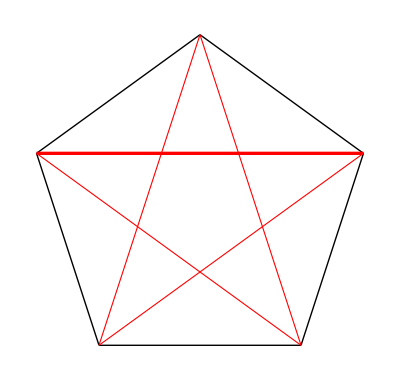

There are 5 ways to inscribe such a line on each face, therefore 5 distinct cubes that can be inscribed within the dodecahedron.

Here are 8 vectors that refer more transparently to the vertices of a cube (in this case a cube of unit radius) than does any such octuple of dodecahedral vertices:

```mathematica
origin={0,0,0};
q11={1,1,1}/(√3);
q12={1,-1,1}/(√3);
q13={-1,-1,1}/(√3);
q14={-1,1,1}/(√3);
q21={1,1,-1}/(√3);
q22={1,-1,-1}/(√3);
q23={-1,-1,-1}/(√3);
q24={-1,1,-1}/(√3);
```

-Graphics3D-

It is evident that the unit vectors q11 and q12 identify adjacent cubic vertices. The cosine the angle between them is given by their dod product:

```mathematica
({q11}.Transpose[{q12}])⟦1⟧⟦1⟧
```

1/3

The obscure property of dodecahedra that Peres asked us to "recall" is seen to be quite a simple property of cubes inscribed within dodecahedra.

Here is a tetrahedron inscribed within a cube:

-Graphics3D-

Notice that edges of the tetrahedron connect next-to-adjacent vertices on the cube, which are next-to-next-to-adjacent vertices on the dodecahedron. A tetrahedron has 6 edges, and each inscribes a diagonal on one of the 6 square faces of the cube, which can be done in two ways.  Therefore 2 distinct tetrahedra that can be inscribed within a cube (the other tetrahedron is defined by the 4 "unused vertices" in the figure), and 2 × 5 = 10 distinct tetrahedra that can be inscribed within a dodecahedron.

The following figure indicates how I propose to name the dodecahedral vertices (how I in fact already named them when I named the 20 vertex vectors P11, P12,  . . . , P45):

-Graphics3D-

The vertices have been grouped in four color-coded 5-member tiers.

For reading off connectivity relations among the dodecahedral vertices it is much easier to work from a planar projection of the preceding 3D figure

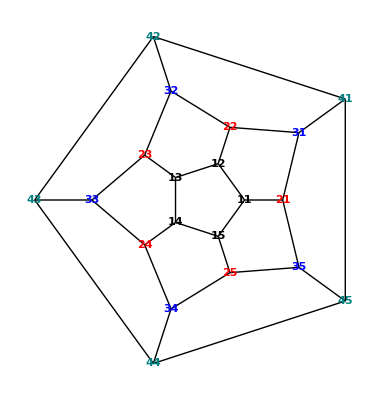

### Penrose's "quintessential trinkets," and orthogonality relations among the 40 rays to which they give rise

Penrose asks us to consider what he calls a "Quintessential Trinket"—a dodecahedral array of measurement devices clustered around a particle with spin 3/2.

-Graphics3D-

The devices—idealized Stern-Gerlach set-ups

```mathematica
Hyperlink["Stern-Gerlach","http://en.wikipedia.org/wiki/Stern-Gerlach_experiment"]
```

—are can be imagined to be positioned at the vertices of the dodecahedron. The device at the a-vertex measures the a-component of spin, and is represented by a matrix of the type discussed previously:

```mathematica
A[a1_, a2_, a3_]:=a1 Subscript[J, 1]+a2 Subscript[J, 2]+a3 Subscript[J, 3]
```

Such a device—if we set ℏ = 1 as we have already agreed to do—would be expected to announce one or another of four numbers

```mathematica
Simplify[Eigenvalues[A[a1,a2,a3]],Assumptions->{a1^2+a2^2+a3^2==1}]
```

{-3/2,-1/2,1/2,3/2}

but has been modified so as to say "ring" if and only if the meter reads 1/2, and in all other cases to say remain silent. What this means—if we look to the spectral resolution of the A-matrix

```mathematica
A[a1, a2, a3]=3/2 Subscript[P, +3/2]+1/2 Subscript[P, +1/2]-1/2 Subscript[P, -1/2]-3/2 Subscript[P, -3/2]
```

—is that the device at the a-vertex is actually represented not by A[a1, a2, a3] but by the projection matrix P_(+1/2)[a1,a2,a3]. We know from previous discussion that that matrix projects onto the "ray" (1-dimensional subspace of 4-dimensional state space) defined by the unit vector F[a1,a2,a3]. I repeat the demonstration

```mathematica
Simplify[A[a1,a2,a3].F[a1,a2,a3]==1/2 F[a1,a2,a3],Assumptions->{a1^2+a2^2+a3^2==1}]
Simplify[Transpose[CompConj[F[a1,a2,a3]]].F[a1,a2,a3],Assumptions->{a1^2+a2^2+a3^2==1}]⟦1⟧⟦1⟧==1
```

True

True

To obtain the projector onto  F[a1, a2, a3]  we have only to construct

```mathematica
Ex[a1_,a2_,a3_]:=F[a1,a2,a3].Transpose[CompConj[F[a1,a2,a3]]]
```

where my Ex notation alludes to the fact that Penrose calls the rays onto which his projectors project "explicit" rays. I demonstrate that the matrix thus defined is in fact projective

```mathematica
Simplify[Ex[a1,a2,a3].Ex[a1,a2,a3]-Ex[a1,a2,a3],Assumptions->{a1^2+a2^2+a3^2==1}]==Subscript[𝕆, 4]
```

True

and does in fact project onto a ray (a one-dimensional subspace of 4-dimensional state space)

```mathematica
Simplify[Eigenvalues[Ex[a1,a2,a3]],Assumptions->{a1^2+a2^2+a3^2==1}]
```

{0,0,0,1}

—namely, onto the ray in question:

```mathematica
Simplify[Ex[a1,a2,a3].F[a1,a2,a3]==F[a1,a2,a3],Assumptions->{a1^2+a2^2+a3^2==1}]
```

True

I want now to extract the components of the normalized vertex vectors—which look typically like this

```mathematica
P11
```

{0.491123,0.356822,0.794654}

—and insert them as arguments into the function Ex[a1, a2, a3]. To that end, I adjust the definition of
 Ex[a1, a2, a3]  to take into account the fact that the arguments will henceforth be not symbolic but numeric

```mathematica
Ex[a1_,a2_,a3_]:=F[a1,a2,a3].Transpose[Conjugate[F[a1,a2,a3]]]
```

define

```mathematica
Ray[X_]:=Ex[X⟦1⟧, X⟦2⟧,X⟦3⟧]
```

and construct

```mathematica
Ex11=Ray[P11]//N//Chop;
Ex12=Ray[P12]//N//Chop;
Ex13=Ray[P13]//N//Chop;
Ex14=Ray[P14]//N//Chop;
Ex15=Ray[P15]//N//Chop;

Ex21=Ray[P21]//N//Chop;
Ex22=Ray[P22]//N//Chop;
Ex23=Ray[P23]//N//Chop;
Ex24=Ray[P24]//N//Chop;
Ex25=Ray[P25]//N//Chop;

Ex31=Ray[P31]//N//Chop;
Ex32=Ray[P32]//N//Chop;
Ex33=Ray[P33]//N//Chop;
Ex34=Ray[P34]//N//Chop;
Ex35=Ray[P35]//N//Chop;

Ex41=Ray[P41]//N//Chop;
Ex42=Ray[P42]//N//Chop;
Ex43=Ray[P43]//N//Chop;
Ex44=Ray[P44]//N//Chop;
Ex45=Ray[P45]//N//Chop;
```

It is gratifying—but no surprise—to discover that these matrices are in fact projective onto rays: selecting one at random, we have

```mathematica
Ex11.Ex11-Ex11//Chop//MatrixForm
Eigenvalues[Ex11]//Chop
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

{1.,0,0,0}

The 20 Ex-projectors serve to identify 20 "explicit rays" in 4-dimensional state space (one associated with each dodecahedral vertex). The nearest neighbors ●●● of any selected vertex ● are next-to-nearest neighbors of each other

-Graphics3D-

and the explicit rays associated with those points are known by construction to be orthogonal. Consider, for example, the case 11 | 12 | 15 | 21 : the blue projectors are mutually orthogonal

```mathematica
Chop[Ex12.Ex15]==Subscript[𝕆, 4]
Chop[Ex15.Ex21]==Subscript[𝕆, 4]
Chop[Ex21.Ex12]==Subscript[𝕆, 4]
```

True

True

True

and therefore necessarily commute (meaning: refer to compatable observables):

```mathematica
Chop[Comm[Ex12,Ex15]]==Subscript[𝕆, 4]
Chop[Comm[Ex15,Ex21]]==Subscript[𝕆, 4]
Chop[Comm[Ex21,Ex12]]==Subscript[𝕆, 4]
```

True

True

True

Simultaneously orthogonal to {Ex12, Ex15, Ex21} if the projection matrix

```mathematica
Im11=Subscript[𝕀, 4]-Ex12-Ex15-Ex21;
```

which is necessarily projective onto a 1-space, the "implicit ray" associated with the vertex 11, the "selected vertex" of which {12, 15, 21} are nearest neighbors. I demonstrate that Im11 does in fact possess the projective  properties just claimed:

```mathematica
Chop[Im11.Im11-Im11]==Subscript[𝕆, 4]
Chop[Eigenvalues[Im11]]
```

True

{1.,0,0,0}

Proceding now from this figure

-Graphics-

I complete the set of implicit projectors:

```mathematica
Im11=Subscript[𝕀, 4]-Ex15-Ex21-Ex12;
Im12=Subscript[𝕀, 4]-Ex11-Ex22-Ex13;
Im13=Subscript[𝕀, 4]-Ex12-Ex23-Ex14;
Im14=Subscript[𝕀, 4]-Ex13-Ex24-Ex15;
Im15=Subscript[𝕀, 4]-Ex14-Ex25-Ex11;

Im21=Subscript[𝕀, 4]-Ex11-Ex35-Ex31;
Im22=Subscript[𝕀, 4]-Ex12-Ex31-Ex32;
Im23=Subscript[𝕀, 4]-Ex13-Ex32-Ex33;
Im24=Subscript[𝕀, 4]-Ex14-Ex33-Ex34;
Im25=Subscript[𝕀, 4]-Ex15-Ex34-Ex35;

Im31=Subscript[𝕀, 4]-Ex41-Ex22-Ex21;
Im32=Subscript[𝕀, 4]-Ex42-Ex23-Ex22;
Im33=Subscript[𝕀, 4]-Ex43-Ex24-Ex23;
Im34=Subscript[𝕀, 4]-Ex44-Ex25-Ex24;
Im35=Subscript[𝕀, 4]-Ex45-Ex21-Ex25;

Im41=Subscript[𝕀, 4]-Ex31-Ex45-Ex42;
Im42=Subscript[𝕀, 4]-Ex32-Ex41-Ex43;
Im43=Subscript[𝕀, 4]-Ex33-Ex42-Ex44;
Im44=Subscript[𝕀, 4]-Ex34-Ex43-Ex45;
Im45=Subscript[𝕀, 4]-Ex35-Ex44-Ex41;
```

We have now in hand—as fruit of Penrose's dodecahedral array of 20 projectors—a population of 40 rays (of which 20 are explicit, 20 implicit) in 4-dimensional state space, from which we have thus far assembled 20 distinct "natural tetrads." Here are 10 of them

```mathematica
{{11, 12, 15, 21}, {12, 13, 11, 22}, {13, 14, 12, 23}, {14, 15, 13, 24}, {15, 11, 14, 25}, {21, 11, 35, 31}, {22, 12, 31, 32}, {23, 13, 32, 33}, {24, 14, 33, 34}, {25, 15, 34, 35}}
```

and here—constructed with the aid of the following list of antipodal vertices

```mathematica
{{11, 12, 13, 14, 15, 21, 22, 23, 24, 25}, {43, 44, 45, 41, 42, 33, 34, 35, 31, 32}}
```

—is a list of the natural tetrads antipodal to those:

```mathematica
{{43, 44, 42, 33}, {44, 45, 43, 34}, {45, 41, 44, 35}, {41, 42, 45, 31}, {42, 43, 41, 32}, {33, 43, 23, 24}, {34, 44, 24, 25}, {35, 45, 25, 21}, {31, 41, 21, 22}, {32, 42, 22, 23}}
```

In both lists, the red entries are implicit, the black entries are explicit.

Thus far we have concerned ourselves with the mutual orthogonality of the Ex projectors associated with trios of mutually next-to-adjacent vertices (and with their shared orthogonality to the Im associated with the vertex at the center of the trio)—the discussion being inspired by the red leg of this figure

-Graphics-

Consider now the neglected blue leg of the figure: it asserts that the Ex associated with a vertix is orthogonal to the Ex associated with the antipodal vertex. Less obviously, the Im associated with vertex—though designed to be orthogonal to the Ex projectors associated with the vertices adjacent to that vertex—is orthogonal also to the Ex at the vertex. Thus

```mathematica
Chop[Ex11.Ex43]==Subscript[𝕆, 4]

Chop[Ex11.Im11]==Subscript[𝕆, 4]
```

True

True

Still less obviously, orthogonal to each of the three projectors mentioned just above is the Im projector associated with the antipodal vertex, which is to say: we have in {Ex11, Im11, ExEx43, Im43} a complete set of orthogonal projectors:

```mathematica
Chop[Ex11+Im11+Ex43+Im43]==Subscript[𝕀, 4]
```

True

```mathematica
Chop[Ex11.Im11]==Subscript[𝕆, 4]
Chop[Ex11.Ex43]==Subscript[𝕆, 4]
Chop[Ex11.Im43]==Subscript[𝕆, 4]
Chop[Im11.Ex43]==Subscript[𝕆, 4]
Chop[Im11.Im43]==Subscript[𝕆, 4]
Chop[Ex43.Im43]==Subscript[𝕆, 4]
```

True

True

True

«3 more identical outputs»

We are led by this remark to a list of 10 "antipodal tetrads":

```mathematica
{{11, 11, 43, 43}, {12, 12, 44, 44}, {13, 13, 45, 45}, {14, 14, 41, 41}, {15, 15, 42, 42}, {21, 21, 33, 33}, {22, 22, 34, 34}, {23, 23, 35, 35}, {24, 24, 31, 31}, {25, 25, 32, 32}}
```

Additionally (and again non-obvioiusly), the implicit projectors associated with the four vertices of any of the 10 inscribed tetrahedra are mutually orthogonal and complete. Look, for example, to the tetrahedron 11 | 24 | 32 | 45, where we find

```mathematica
Chop[Im11.Im24]==Subscript[𝕆, 4]
Chop[Im11.Im32]==Subscript[𝕆, 4]
Chop[Im11.Im45]==Subscript[𝕆, 4]
Chop[Im24.Im32]==Subscript[𝕆, 4]
Chop[Im24.Im45]==Subscript[𝕆, 4]
Chop[Im32.Im45]==Subscript[𝕆, 4]
Chop[Im11+Im24+Im32+Im45]==Subscript[𝕀, 4]
```

True

True

True

«4 more identical outputs»

We are led by this remark to a list of 10 "tetrahedral tetrads":

```mathematica
{{11, 24, 32, 45}, {11, 23, 34, 41}, {12, 25, 33, 41}, {12, 24, 35, 42}, {13, 21, 34, 42}, {13, 25, 31, 43}, {14, 22, 35, 43}, {14, 21, 32, 44}, {15, 23, 31, 44}, {15, 22, 33, 45}}
```

So from our 40 designated rays in 4-space (20 explicit, 20 implicit) we have assembled 40 tetrads (20 natural, 10 antipodal, 10 tetrahedral). We discover by counting that every explicit/implicit ray is a member simultaneously of 4 such tetrads, and is orthogonal to 12 of the 16 rays from which those tetrads are assembled. Here, by way of illustration, I list the rays orthogonal to (respectively) 11 and 11:

```mathematica
{{11, orthogonal to, 11, 12, 14, 15, 21, 22, 23, 25, 31, 35, 43, 43}}
```

```mathematica
{{11, orthogonal to, 11, 12, 15, 21, 23, 24, 32, 34, 41, 43, 43, 45}}
```

### The matrices the represent the action of "vertex buttons"

Generally, to describe the state-transforming action of the measurement device represented by the hermitian matrix 𝔸 we look to the spectral resolution of 𝔸:

```mathematica
𝔸=Subscript[λ, 1] Subscript[ℙ, 1]+Subscript[λ, 2] Subscript[ℙ, 2]+⋯+Subscript[λ, n] Subscript[ℙ, n]
```

When Ψ is presented to the meter, it
     • produces (then normalizes) ℙ_1 Ψ and (with probability |ℙ_1 Ψ|^2 ) announces λ_1, or else
     • produces (then normalizes) ℙ_2 Ψ and (with probability |ℙ_2 Ψ|^2 ) announces λ_2, or else . . . etc.

The point of this remark is to emphasize that the projector Ex at a vertex cannot by itself describe the action of the meter (button) at that vertex, for if it did then states normal to the eplicit ray onto which Ex projects would be extinguished by the act of measurement. Which is something that quantum measurements never do. No, we must write something like

```mathematica
Subscript[Button, 11]=Subscript[λ, 1] Subscript[Ex, 11]+Subscript[λ, 2](𝕀-Subscript[Ex, 11])
```

to describe the action of the button. It announces  λ_1 (and rings a bell) and creates/normalizes the state Ex_11 Ψ, or else announces λ_2 (and remains silent) and creates/normalizes a state orthogonal to the explicit ray associated with that vertex. It is for this reason that we will soon acquire interest in the complements of the Ex projectors.

### Setting things up so Alice and Bob can do some quantum mechanics

Penrose stipulates that his Quintessential Trinckets are to be manufactured in identical, serial numbered pairs. One member of each pair is delivered to Alice's lab, its mate to Bob's far-away lab, producing the situation illustrated below:

-Graphics-

If Alice/Bob's particles were independent we would write

```mathematica
Ψ=({{Subscript[α, 1]}, {Subscript[α, 2]}, {Subscript[α, 3]}, {Subscript[α, 4]}})⊗({{Subscript[β, 1]}, {Subscript[β, 2]}, {Subscript[β, 3]}, {Subscript[β, 4]}});
```

```mathematica
Ψ//MatrixForm
```

(α_1 β_1
α_1 β_2
α_1 β_3
α_1 β_4
α_2 β_1
α_2 β_2
α_2 β_3
α_2 β_4
α_3 β_1
α_3 β_2
α_3 β_3
α_3 β_4
α_4 β_1
α_4 β_2
α_4 β_3
α_4 β_4)

to describe the state of the composite system. The quantum effects of present interest arise, however, from the assumption that the two particles are in an entangled state (actually, a particular instance of an entangled state), a state

```mathematica
Ψ=({{Subscript[ψ, 1]}, {Subscript[ψ, 2]}, {Subscript[ψ, 3]}, {Subscript[ψ, 4]}, {Subscript[ψ, 5]}, {Subscript[ψ, 6]}, {Subscript[ψ, 7]}, {Subscript[ψ, 8]}, {Subscript[ψ, 9]}, {Subscript[ψ, 10]}, {Subscript[ψ, 11]}, {Subscript[ψ, 12]}, {Subscript[ψ, 13]}, {Subscript[ψ, 14]}, {Subscript[ψ, 15]}, {Subscript[ψ, 16]}})
```

that is "non-separable" in the sense that it does not admit of Kronecker factorization.

We are about to acquire need of some expanded definitions

```mathematica
Subscript[𝕆, 16]=Subscript[𝕆, 4]⊗Subscript[𝕆, 4];
Subscript[𝕀, 16]=Subscript[𝕀, 4]⊗Subscript[𝕀, 4];
```

and of this property of Kronecker products

```mathematica
(𝔸⊗𝔹).(ℂ⊗𝔻)=(𝔸.ℂ)⊗(𝔹.𝔻)
```

which is valid whenever it makes sense.

The action of (say) Alice's 11 button—describe when she worked in solitude by the 4 × 4 matrix

```mathematica
Subscript[α, 1] Ex11+Subscript[α, 2](Subscript[𝕀, 4]-Ex11)
```

—has now to be described by the 16 × 16 matrix

```mathematica
(Subscript[α, 1] Ex11+Subscript[α, 2](Subscript[𝕀, 4]-Ex11))⊗Subscript[𝕀, 4]=Subscript[α, 1](Ex11⊗Subscript[𝕀, 4])+Subscript[α, 2](Subscript[𝕀, 16]-(Ex11⊗Subscript[𝕀, 4]))
```

which we notate

```mathematica
Subscript[α, 1] A11+Subscript[α, 2] a11
```

with

```mathematica
A11=Ex11⊗Subscript[𝕀, 4];
a11=Subscript[𝕀, 16]-A11;
```

It now follows from the fact that Ex11 and 𝕀 are projective that so also is A11 (whence also its complement, a11):

```mathematica
Chop[A11.A11-A11]==Subscript[𝕆, 16]
```

True

A11 projects onto a 4-dimensional subspace of 16-dimensional "composite state space":

```mathematica
Eigenvalues[A11]//Chop
```

{1.,1.,1.,1.,0,0,0,0,0,0,0,0,0,0,0,0}

Bob's buttons are represented by matrices of the complementary form

```mathematica
Subscript[β, 1] B11+Subscript[β, 2] b11
```

with

```mathematica
B11=Subscript[𝕀, 4]⊗Ex11;
b11=Subscript[𝕀, 16]-B11;
```

I now construct a complete list of the 16 × 16 matrices that enter into the representation of Alice's buttons

```mathematica
A11=Ex11⊗Subscript[𝕀, 4];
A12=Ex12⊗Subscript[𝕀, 4];
A13=Ex13⊗Subscript[𝕀, 4];
A14=Ex14⊗Subscript[𝕀, 4];
A15=Ex15⊗Subscript[𝕀, 4];

A21=Ex21⊗Subscript[𝕀, 4];
A22=Ex22⊗Subscript[𝕀, 4];
A23=Ex23⊗Subscript[𝕀, 4];
A24=Ex24⊗Subscript[𝕀, 4];
A25=Ex25⊗Subscript[𝕀, 4];

A31=Ex31⊗Subscript[𝕀, 4];
A32=Ex32⊗Subscript[𝕀, 4];
A33=Ex33⊗Subscript[𝕀, 4];
A34=Ex34⊗Subscript[𝕀, 4];
A35=Ex35⊗Subscript[𝕀, 4];

A41=Ex41⊗Subscript[𝕀, 4];
A42=Ex42⊗Subscript[𝕀, 4];
A43=Ex43⊗Subscript[𝕀, 4];
A44=Ex44⊗Subscript[𝕀, 4];
A45=Ex45⊗Subscript[𝕀, 4];

a11=Subscript[𝕀, 16]-A11;
a12=Subscript[𝕀, 16]-A12;
a13=Subscript[𝕀, 16]-A13;
a14=Subscript[𝕀, 16]-A14;
a15=Subscript[𝕀, 16]-A15;

a21=Subscript[𝕀, 16]-A21;
a22=Subscript[𝕀, 16]-A22;
a23=Subscript[𝕀, 16]-A23;
a24=Subscript[𝕀, 16]-A24;
a25=Subscript[𝕀, 16]-A25;

a31=Subscript[𝕀, 16]-A31;
a32=Subscript[𝕀, 16]-A32;
a33=Subscript[𝕀, 16]-A33;
a34=Subscript[𝕀, 16]-A34;
a35=Subscript[𝕀, 16]-A35;

a41=Subscript[𝕀, 16]-A41;
a42=Subscript[𝕀, 16]-A42;
a43=Subscript[𝕀, 16]-A43;
a44=Subscript[𝕀, 16]-A44;
a45=Subscript[𝕀, 16]-A45;
```

and do also the same thing for Bob:

```mathematica
B11=Subscript[𝕀, 4]⊗Ex11;
B12=Subscript[𝕀, 4]⊗Ex12;
B13=Subscript[𝕀, 4]⊗Ex13;
B14=Subscript[𝕀, 4]⊗Ex14;
B15=Subscript[𝕀, 4]⊗Ex15;

B21=Subscript[𝕀, 4]⊗Ex21;
B22=Subscript[𝕀, 4]⊗Ex22;
B23=Subscript[𝕀, 4]⊗Ex23;
B24=Subscript[𝕀, 4]⊗Ex24;
B25=Subscript[𝕀, 4]⊗Ex25;

B31=Subscript[𝕀, 4]⊗Ex31;
B32=Subscript[𝕀, 4]⊗Ex32;
B33=Subscript[𝕀, 4]⊗Ex33;
B34=Subscript[𝕀, 4]⊗Ex34;
B35=Subscript[𝕀, 4]⊗Ex35;

B41=Subscript[𝕀, 4]⊗Ex41;
B42=Subscript[𝕀, 4]⊗Ex42;
B43=Subscript[𝕀, 4]⊗Ex43;
B44=Subscript[𝕀, 4]⊗Ex44;
B45=Subscript[𝕀, 4]⊗Ex45;

b11=Subscript[𝕀, 16]-B11;
b12=Subscript[𝕀, 16]-B12;
b13=Subscript[𝕀, 16]-B13;
b14=Subscript[𝕀, 16]-B14;
b15=Subscript[𝕀, 16]-B15;

b21=Subscript[𝕀, 16]-B21;
b22=Subscript[𝕀, 16]-B22;
b23=Subscript[𝕀, 16]-B23;
b24=Subscript[𝕀, 16]-B24;
b25=Subscript[𝕀, 16]-B25;

b31=Subscript[𝕀, 16]-B31;
b32=Subscript[𝕀, 16]-B32;
b33=Subscript[𝕀, 16]-B33;
b34=Subscript[𝕀, 16]-B34;
b35=Subscript[𝕀, 16]-B35;

b41=Subscript[𝕀, 16]-B41;
b42=Subscript[𝕀, 16]-B42;
b43=Subscript[𝕀, 16]-B43;
b44=Subscript[𝕀, 16]-B44;
b45=Subscript[𝕀, 16]-B45;
```

### Construction of the "singlet state" of a composite pair of spin 3/2 particles

The spin operators for composite pairs of spin  3/2 particles are constructed as follows:

```mathematica
Subscript[JJ, 1]=(Subscript[J, 1]⊗Subscript[𝕀, 4])+(Subscript[𝕀, 4]⊗Subscript[J, 1]);
Subscript[JJ, 2]=(Subscript[J, 2]⊗Subscript[𝕀, 4])+(Subscript[𝕀, 4]⊗Subscript[J, 2]);
Subscript[JJ, 3]=(Subscript[J, 3]⊗Subscript[𝕀, 4])+(Subscript[𝕀, 4]⊗Subscript[J, 3]);
```

They have this typical appearance

```mathematica
Subscript[JJ, 1]//MatrixForm
```

(0 | (√3)/2 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(√3)/2 | 0 | 1 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | (√3)/2 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (√3)/2 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(√3)/2 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (√3)/2 | 0 | 0 | (√3)/2 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (√3)/2 | 0 | 0 | 1 | 0 | (√3)/2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3)/2 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | 0 | (√3)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | (√3)/2 | 0 | 1 | 0 | 0 | (√3)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | (√3)/2 | 0 | 0 | (√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | 0 | (√3)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | 0 | (√3)/2 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | 0 | 1 | 0 | (√3)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | 0 | 0 | (√3)/2 | 0)

and certainly too large to manipulate by hand: to multiply two such matrices (which—happily—are fairly sparce) requires that 16 multiplications followed by 16 additions be performed 16^2= 256 times, for a total of 8192 operations. But Mathematica verifies that the matrices do possess the anticipated commutation relations

```mathematica
Comm[Subscript[JJ, 1],Subscript[JJ, 2]]==ⅈ ℏ Subscript[JJ, 3]
Comm[Subscript[JJ, 2],Subscript[JJ, 3]]==ⅈ ℏ Subscript[JJ, 1]
Comm[Subscript[JJ, 3],Subscript[JJ, 1]]==ⅈ ℏ Subscript[JJ, 2]
```

True

True

True

in which connection it will be recalled that we have set ℏ = 1. Introducing  the square of the total spin

```mathematica
JJJJ=Subscript[JJ, 1].Subscript[JJ, 1]+Subscript[JJ, 2].Subscript[JJ, 2]+Subscript[JJ, 3].Subscript[JJ, 3];
```

we obtain the anticipated commutation relations

```mathematica
Comm[JJJJ,Subscript[JJ, 1]]==Subscript[𝕆, 16]
Comm[JJJJ,Subscript[JJ, 2]]==Subscript[𝕆, 16]
Comm[JJJJ,Subscript[JJ, 3]]==Subscript[𝕆, 16]
```

Both of the 16 ×16 hermitian matrices  JJ_3  and JJJJ  possess degenerate spectra

```mathematica
Eigenvalues[Subscript[JJ, 3]]
Eigenvalues[JJJJ]
```

{-3,3,-2,-2,2,2,-1,-1,-1,1,1,1,0,0,0,0}

{12,12,12,12,12,12,12,6,6,6,6,6,2,2,2,0}

but we are not surprised to discover that each serves to resolve the degeneracy of the other. For,  recalling that the quantum theory of angular momentum supplies the pattern

```mathematica
L^2 Subscript[Y, λ m]=ℏ^2 λ(λ+1)Subscript[Y, λ m]:    λ∈{0,1/2,1,3/2,2,5/2,...}
Subscript[L, 3] Subscript[Y, λ m]=ℏ m Subscript[Y, λ m]                      :    m∈{-λ,...,0,...,+λ}
```

we see from

```mathematica
Solve[ℏ^2 λ(λ+1)==2 ℏ^2,λ]
Solve[ℏ^2 λ(λ+1)==6 ℏ^2,λ]
Solve[ℏ^2 λ(λ+1)==12 ℏ^2,λ]
```

{{λ→-2},{λ→1}}

{{λ→-3},{λ→2}}

{{λ→-4},{λ→3}}

that the spin properties of a composite pair of spin 3/2 particles are those illustrated in the following figure

-Graphics-

which signals that a composite pair of red systems ● is equivalent to a single copy of the black ● system. With each of the 16 black dots we associate one member of a certain doubly-indexed orthonormal basis in 16-dimensional complex space. Intuition informs me that I will have greatest interest in the singlet at the bottom of the inverted pyramid, and that it will be some kind of "generalized Bell state." 

In "Penrose Dodecahedron: Part I" I show that eigenstates

```mathematica
up=({{1}, {0}});
dn=({{0}, {1}});
```

of

```mathematica
Subscript[σ, 3]=({{1, 0}, {0, -1}})
```

can be used to construct eigenstates

```mathematica
u3=up⊗up;
u1=up⊗dn;
d1=dn⊗up;
d3=dn⊗dn;
```

of

```mathematica
Subscript[J, 3]//MatrixForm
```

(3/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -3/2)

Sixteen simple linear combinations of Kronecker products of the 4-vectors u3, u1, d1  and d3 are shown there to comprise simultaneous eigenvectors of JJ_3 and JJJJ. In particular, we are led to define

```mathematica
u3d3m=(u3⊗d3-d3⊗u3)/(√2);
u1d1m=(u1⊗d1-d1⊗u1)/(√2);
```

(the final m means "minus": some related vectors have names that end in p, signifying "plus") and from those to assemble

```mathematica
singlet=(u3d3m-u1d1m)/(√2);
```

of which

```mathematica
singlet=((↑↑↑)⊗(↓↓↓)-(↓↓↓)⊗(↑↑↑)-(↑↑↓)⊗(↓↓↑)+(↓↓↑)⊗(↑↑↓))/(√2)
```

provides a more picturesque—if (to me) less intelligible—description. In this connection see page 297 in Penrose's Shadows of the Mind.  The state-vector thus defined certainly does appear, on its face, to be non-separable (entangled) and to have much in common with the simpler structures known as "Bell states."

The short of it is this: the 16-vector

```mathematica
singlet//MatrixForm
```

(0
0
0
1/2
0
0
-1/2
0
0
1/2
0
0
-1/2
0
0
0)

demonstrably does possess precisely the properties we expect of the singlet state:

```mathematica
JJJJ.singlet==0 singlet
Subscript[JJ, 3].singlet==0 singlet
```

True

True

Now that we are in 16-space, we will soon have need also of the definition

```mathematica
Subscript[ZeroVector, 16]=({{0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
```

### The experimental protocol (which we may think of as a game)

Alice selects a vertex ● arbitrarly, which places the three adjacent buttons ●●● in play: they can be played in any sequence, since they perform compatible operations (represented by commutative matrices). The rotational symmetry of the system means that we can without loss of generality assume she selects the 11 vertex, and plays the 12 | 15 | 21 buttons. Bob does the same. We are obliged to consider six cases:
	• Bob's ● is the same as Alice's (unique);
	• Bob's ● is a adjacent to Alice's (3 possibilities);
	• Bob's ● is a next-to-adjacent (cubically adjacent) to Alice's (6 possibilities);
	• Bob's ● is a next-to-adjacent (cubically adjacent) to Alice's to Alice's antipode
	 (= tetrahedrally adjacent to Alice's vertex: 6 possibilities);
	• Bob's ● is adjacent to Alice's antipode (3 possibilities);
	• Bob's ● is antipodal to Alice's (unique)

Bob, in short, has 20 selection options, which fall into 6 classes.

Though the details differ from game to game, the general pattern of events is in all cases the same. Assume the system to be initially in the generic composite state Ψ, and allow Alice to make the first move. Alice presses the A_1 button, and either the bell rings or it doesn't, signaling that the state inherited by Bob is (prior to normalization—an irrelevant detail which I will henceforth neglect)—one or the other of the following:

```mathematica
Subscript[A, 1].Ψ
Subscript[a, 1].Ψ
```

Bob presses the B_1button, and the state available to Alice becomes  one or another of these four

```mathematica
Subscript[B, 1].Subscript[A, 1].Ψ
Subscript[B, 1].Subscript[a, 1].Ψ
Subscript[b, 1].Subscript[A, 1].Ψ
Subscript[b, 1].Subscript[a, 1].Ψ
```

according as Bob's bell did or did not ring. Alice presses A_2 and the surviving state is one or another of the following

```mathematica
Subscript[A, 2].Subscript[B, 1].Subscript[A, 1].Ψ=Subscript[A, 2].Subscript[A, 1].Subscript[B, 1].Ψ=0
Subscript[A, 2].Subscript[B, 1].Subscript[a, 1].Ψ=Subscript[A, 2].Subscript[a, 1].Subscript[B, 1].Ψ
Subscript[A, 2].Subscript[b, 1].Subscript[A, 1].Ψ=Subscript[A, 2].Subscript[A, 1].Subscript[b, 1].Ψ=0
Subscript[A, 2].Subscript[b, 1].Subscript[a, 1].Ψ=Subscript[A, 2].Subscript[a, 1].Subscript[b, 1].Ψ
Subscript[a, 2].Subscript[B, 1].Subscript[A, 1].Ψ=Subscript[a, 2].Subscript[A, 1].Subscript[B, 1].Ψ
Subscript[a, 2].Subscript[B, 1].Subscript[a, 1].Ψ=Subscript[a, 2].Subscript[a, 1].Subscript[B, 1].Ψ
Subscript[a, 2].Subscript[b, 1].Subscript[A, 1].Ψ=Subscript[a, 2].Subscript[A, 1].Subscript[b, 1].Ψ
Subscript[a, 2].Subscript[b, 1].Subscript[a, 1].Ψ=Subscript[a, 2].Subscript[a, 1].Subscript[b, 1].Ψ
```

Here it is the fact that all (A or a)-matrices commute with all (B or b)-matrices that has permitted the rearrangement of the matrix factors on the right, and it is the fact that all next-to-adjacent (cubically adjacent) A-matrices are orthogonal (ditto for B-matrices, but not for a, b-matrices) that has rendered two of the seeming possibilities impossible.

The commutivity circumstances just mentioned mean that Alice and Bob (who are in no position to arrange to move alternately, since they must complete the game before a signal could pass from one to the other) can make their moves in any order. And from fact that the buttons Alice (same for Bob) has in play refer to mutually orthogonal rays it follows that neither player will ever ring two bells in the same game: its none or one.  

Here, therefore, is a list of all the ways in which the initial state Ψ might be transformed by the time Alice and Bob have finished playing the game:

```mathematica
Subscript[a, 1].Subscript[a, 2].Subscript[a, 3].Subscript[b, 1].Subscript[b, 2].Subscript[b, 3].Ψ
Subscript[A, 1].Subscript[a, 2].Subscript[a, 3].Subscript[b, 1].Subscript[b, 2].Subscript[b, 3].Ψ
Subscript[a, 1].Subscript[A, 2].Subscript[a, 3].Subscript[b, 1].Subscript[b, 2].Subscript[b, 3].Ψ
Subscript[a, 1].Subscript[a, 2].Subscript[A, 3].Subscript[b, 1].Subscript[b, 2].Subscript[b, 3].Ψ

Subscript[a, 1].Subscript[a, 2].Subscript[a, 3].Subscript[B, 1].Subscript[b, 2].Subscript[b, 3].Ψ
Subscript[A, 1].Subscript[a, 2].Subscript[a, 3].Subscript[B, 1].Subscript[b, 2].Subscript[b, 3].Ψ
Subscript[a, 1].Subscript[A, 2].Subscript[a, 3].Subscript[B, 1].Subscript[b, 2].Subscript[b, 3].Ψ
Subscript[a, 1].Subscript[a, 2].Subscript[A, 3].Subscript[B, 1].Subscript[b, 2].Subscript[b, 3].Ψ

Subscript[a, 1].Subscript[a, 2].Subscript[a, 3].Subscript[b, 1].Subscript[B, 2].Subscript[b, 3].Ψ
Subscript[A, 1].Subscript[a, 2].Subscript[a, 3].Subscript[b, 1].Subscript[B, 2].Subscript[b, 3].Ψ
Subscript[a, 1].Subscript[A, 2].Subscript[a, 3].Subscript[b, 1].Subscript[B, 2].Subscript[b, 3].Ψ
Subscript[a, 1].Subscript[a, 2].Subscript[A, 3].Subscript[b, 1].Subscript[B, 2].Subscript[b, 3].Ψ

Subscript[a, 1].Subscript[a, 2].Subscript[a, 3].Subscript[b, 1].Subscript[b, 2].Subscript[B, 3].Ψ
Subscript[A, 1].Subscript[a, 2].Subscript[a, 3].Subscript[b, 1].Subscript[b, 2].Subscript[B, 3].Ψ
Subscript[a, 1].Subscript[A, 2].Subscript[a, 3].Subscript[b, 1].Subscript[b, 2].Subscript[B, 3].Ψ
Subscript[a, 1].Subscript[a, 2].Subscript[A, 3].Subscript[b, 1].Subscript[b, 2].Subscript[B, 3].Ψ
```

Capital letters signal bells that rang, lower case letters signal bells that remained silent. Quantum mechanics provides a mechanism by means of which we could assign probabilities to each such transformation

```mathematica
Subscript[Ψ, initial] ↦ Subscript[Ψ, final]
```

but I won't, since most such information is irrelevant to the problem at hand: we, in our search for persistent patterns, will have interest in probabilities only when they vanish, signaling that events of the sort in question are impossible.

### Patterns that emerge when Penrose's game is played

As remarked earlier, we will, without loss of generality, assume in all cases that Alice has selected the 11 vertex, and will therefore be playing the 12 | 15 | 21 buttons

First game: Bob's selected vertex COINCIDES with Alice's

Alice's buttons | A12 | A15 | A21
Bob's buttons | B12 | B15 | B21

We look to all 16 of the possible sequences of events, conjecturing in each instance that the sequence is impossible. Calculation establishes which of those conjectures are True, which False.

```mathematica
Chop[a12.a15.a21.b12.b15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b12.b15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b12.b15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b12.b15.b21.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.B12.b15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.B12.b15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.B12.b15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.B12.b15.b21.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.b12.B15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b12.B15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b12.B15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b12.B15.b21.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.b12.b15.B21.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b12.b15.B21.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b12.b15.B21.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b12.b15.B21.singlet]==Subscript[ZeroVector, 16]
```

True

False

False

False

«1 more identical outputs»

True

False

False

False

«1 more identical outputs»

True

False

False

False

«1 more identical outputs»

True

The impossible cases (cases with zero probability) are four in number. From this one

```mathematica
Chop[a12.a15.a21.b12.b15.b21.singlet]==Subscript[ZeroVector, 16]
```

True

we learn that if Alice and Bob SELECT THE SAME VERTEX then it is impossible for neither Alice nor Bob to ring a bell by game's end.  From

```mathematica
Chop[A12.a15.a21.B12.b15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b12.B15.b21.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b12.b15.B21.singlet]==Subscript[ZeroVector, 16]
```

True

True

True

we learn that, while it is possible for both to ring, it is impossible for them to ring bells on identical vertices.

Same-vertex-selection is not the only circumstance that can lead Alice and Bob to share a button: it happens also (but only once) if they select cubically adjacent (nex-nearest-neighboring) buttons.  I digress to establish that what I call the

DIGRESSION: Principle of the Poisoned Vertex

holds quite generally. I look to only the first four of a set of sixteen statements:

```mathematica
Chop[A11.B11.singlet]==Subscript[ZeroVector, 16]
Chop[A12.B12.singlet]==Subscript[ZeroVector, 16]
Chop[A13.B13.singlet]==Subscript[ZeroVector, 16]
Chop[A14.B14.singlet]==Subscript[ZeroVector, 16]
Chop[A15.B15.singlet]==Subscript[ZeroVector, 16]
```

True

True

True

«2 more identical outputs»

The fact that if a button rings for one player it cannot ring for the other hinges critically upon a property of the singlet state, as I demonstrate: if we replace the singlet with (for example)

```mathematica
Subscript[TypicalNonSinglet, 16]=({{1}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
```

the "poisoned vertex principle" is lost:

```mathematica
Chop[A11.B11.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A12.B12.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A13.B13.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A14.B14.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A15.B15.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
```

False

False

False

«2 more identical outputs»

Finally, if a player gets no ring at a given vertex then no restriction is placed upon what the other player can experience at that vertex, as these examples make clear:

```mathematica
Chop[a11.B11.singlet]==Subscript[ZeroVector, 16]
Chop[a12.b12.singlet]==Subscript[ZeroVector, 16]
```

False

False

Second game: Bob's selected vertex is ADJACENT to Alice's

We consider the case in which Bob selects nearest neighbor 12.

Alice's buttons | A12 | A15 | A21
Bob's buttons | B11 | B22 | B13

```mathematica
Chop[a12.a15.a21.b11.b22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b11.b22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b11.b22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b11.b22.b13.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.B11.b22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.B11.b22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.B11.b22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.B11.b22.b13.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.b11.B22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b11.B22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b11.B22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b11.B22.b13.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.b11.b22.B13.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b11.b22.B13.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b11.b22.B13.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b11.b22.B13.singlet]==Subscript[ZeroVector, 16]
```

False

True

False

False

True

False

False

False

«2 more identical outputs»

True

False

False

False

«1 more identical outputs»

True

There are again four impossible cases. From

```mathematica
Chop[A12.a15.a21.b11.b22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.a21.B11.b22.b13.singlet]==Subscript[ZeroVector, 16]
```

True

True

we learn that if Alice/Bob's SELECTED VERTICES ARE ADJACENT and if Alice gets a ring on Bob's vertex, then it is impossible for Bob not to get a ring by game's end. And vice versa. Bringing to

```mathematica
Chop[a12.A15.a21.b11.B22.b13.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b11.b22.B13.singlet]==Subscript[ZeroVector, 16]
```

True

True

the observation that both {15, 22} and {21, 13} identify tetrahedrally adjacent vertices (next-to-next-nearest neighbors) we get the first hint of a general principle which I digress now to prove.

DIGRESSION: Principle of Tetrahedral Exclusion

Each row in the following table presents a list of the 8 vertices of one of the 5 cubes that are inscribed within the dodecahedron. The red entries in that row list the vertices in one of the tetrahedra inscribed within that cube, and the black entries identify the other tetrahedon.

```mathematica
{{11, 13, 24, 25, 45, 31, 32, 43}, {12, 14, 33, 32, 41, 21, 25, 44}, {13, 15, 21, 22, 42, 33, 34, 45}, {14, 11, 22, 23, 43, 34, 35, 41}, {15, 12, 23, 24, 44, 35, 31, 42}}
```

Looking to all vertex pairs in the tetrahedron 11 | 24 | 45 | 32 , I assign one vertex to Alice, the other to Bob and get

```mathematica
Chop[A11.B24.singlet]==Subscript[ZeroVector, 16]
Chop[A11.B45.singlet]==Subscript[ZeroVector, 16]
Chop[A11.B32.singlet]==Subscript[ZeroVector, 16]
Chop[A24.B45.singlet]==Subscript[ZeroVector, 16]
Chop[A24.B32.singlet]==Subscript[ZeroVector, 16]
Chop[A45.B32.singlet]==Subscript[ZeroVector, 16]
```

True

True

True

«3 more identical outputs»

So it would go with each of the other nine tetrahedra. Here again we encounter a general principle that hinges upon a special property of the singlet state. For if we abandon the singlet the "principle of tetrahedral exclusion" lost:

```mathematica
Chop[A11.B24.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A11.B45.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A11.B32.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A24.B45.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A24.B32.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A45.B32.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
```

False

False

False

«3 more identical outputs»

The upshot of the principle is that it is impossible for Bob—whatever might be his selected vertex and its relationship to Alice's—to ring at a vertex that is tetrahedrally related to a vertex at which Alice rang, and vice versa.

Third game: Bob's selected vertex is CUBICALLY ADJACENT (next-nearest) to Alice's

We consider the case in which Bob selects nest-nearest neighbor 22.

Alice's buttons | A12 | A15 | A21
Bob's buttons | B12 | B31 | B32

```mathematica
Chop[a12.a15.a21.b12.b31.b32.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b12.b31.b32.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b12.b31.b32.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b12.b31.b32.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.B12.b31.b32.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.B12.b31.b32.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.B12.b31.b32.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.B12.b31.b32.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.b12.B31.b32.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b12.B31.b32.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b12.B31.b32.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b12.B31.b32.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.b12.b31.B32.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b12.b31.B32.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b12.b31.B32.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b12.b31.B32.singlet]==Subscript[ZeroVector, 16]
```

True

False

False

False

«1 more identical outputs»

True

False

False

False

«1 more identical outputs»

True

False

False

False

«1 more identical outputs»

True

From the first of the four impossible cases

```mathematica
Chop[a12.a15.a21.b12.b31.b32.singlet]==Subscript[ZeroVector, 16]

Chop[A12.a15.a21.B12.b31.b32.singlet]==Subscript[ZeroVector, 16]

Chop[a12.A15.a21.b12.B31.b32.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b12.b31.B32.singlet]==Subscript[ZeroVector, 16]
```

True

True

True

«1 more identical outputs»

we learn that if the vertices selected by Alice/Bob are cubically adjacent then it is, once again, impossible for neither player to ring a bell by games end. The second case provides an illustration of the poisoned vertex principle, while the  last two cases illustrate the principle of tetrahedral exclusion.

Third game: Bob's selected vertex is ANTIPODAL to Alice's

Alice's buttons | A12 | A15 | A21
Bob's buttons | B33 | B42 | B44

```mathematica
Chop[a12.a15.a21.b33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b33.b42.b44.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.B33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.B33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.B33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.B33.b42.b44.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.b33.B42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b33.B42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b33.B42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b33.B42.b44.singlet]==Subscript[ZeroVector, 16]

Chop[a12.a15.a21.b33.b42.B44.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b33.b42.B44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b33.b42.B44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b33.b42.B44.singlet]==Subscript[ZeroVector, 16]
```

False

True

True

True

«3 more identical outputs»

False

True

True

False

True

True

False

True

True

The impossibility in six of those twelve cases

```mathematica
Chop[A12.a15.a21.B33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[A12.a15.a21.b33.B42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.B33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b33.b42.B44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b33.B42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b33.b42.B44.singlet]==Subscript[ZeroVector, 16]
```

True

True

True

«3 more identical outputs»

can be attributed to the principle of tetrahedral exclusion, as we see by consulting again this list of tetrahedral vertexes:

```mathematica
{{11, 13, 24, 25, 45, 31, 32, 43}, {12, 14, 33, 32, 41, 21, 25, 44}, {13, 15, 21, 22, 42, 33, 34, 45}, {14, 11, 22, 23, 43, 34, 35, 41}, {15, 12, 23, 24, 44, 35, 31, 42}}
```

From the remaining six cases

```mathematica
Chop[A12.a15.a21.b33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.A15.a21.b33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.A21.b33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.a21.B33.b42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.a21.b33.B42.b44.singlet]==Subscript[ZeroVector, 16]
Chop[a12.a15.a21.b33.b42.B44.singlet]==Subscript[ZeroVector, 16]
```

True

True

True

«3 more identical outputs»

we conclude that if Alice and Bob have selected antipodal vertices, then if one gets a ring it is impossible for the other not to: either neither gets a ring or both do. We have already discovered, however, that if Alice rings at 12 then it is—by the principle of tetrahedral exclusion—impossible for Bob to ring at either 33 or 42: Bob is obligated to ring at 44, which is antipodal to the button that rang for Alice. This striking result motivates the following

DIGRESSION: Principle of Antipodal Coincidence

may be in force even when Alice/Bob did not select antipodal vertices (the point here being that they may find themselves pressing antipodal buttons even if they did not select antipodal vertices), which I undertake now to prove. Working from this list of antipodal vertices

```mathematica
{{11, 12, 13, 14, 15, 21, 22, 23, 24, 25}, {43, 44, 45, 41, 42, 33, 34, 35, 31, 32}}
```

we have

```mathematica
Chop[A11.b43.singlet]==Subscript[ZeroVector, 16]
Chop[A12.b44.singlet]==Subscript[ZeroVector, 16]
Chop[A13.b45.singlet]==Subscript[ZeroVector, 16]
Chop[A14.b41.singlet]==Subscript[ZeroVector, 16]
Chop[A15.b42.singlet]==Subscript[ZeroVector, 16]
Chop[A21.b33.singlet]==Subscript[ZeroVector, 16]
Chop[A22.b34.singlet]==Subscript[ZeroVector, 16]
Chop[A23.b35.singlet]==Subscript[ZeroVector, 16]
Chop[A24.b31.singlet]==Subscript[ZeroVector, 16]
Chop[A25.b32.singlet]==Subscript[ZeroVector, 16]
```

True

True

True

«7 more identical outputs»

We note in passing that here again we have a result that hinges critically upon a special property of the singlet state:

```mathematica
Chop[A11.b43.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A12.b44.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A13.b45.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A14.b41.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A15.b42.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A21.b33.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A22.b34.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A23.b35.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A24.b31.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
Chop[A25.b32.Subscript[TypicalNonSinglet, 16]]==Subscript[ZeroVector, 16]
```

False

False

False

«7 more identical outputs»

We have thus far studied examples of only three of the six possible game types. There are conclusions to be drawn from the others but we need not look to those games because we have already in hand all that is required to establish Penrose's no-go theorem.

### Enter: the local realist

The local realist postulates that the results obtained by Alice/Bob in any given game were pre-programed into the Quintessential Trinkets used in that game. He interprets the general principles that we extracted from the results of quantum mechanical calculations to reflect constraints that were recognized by the engineers who constructed each individual trinket pair.  

To conform to the "it is impossible for neither Alice nor Bob to ring a bell by game's end" that comes into force when Alice/Bob select either identical or next-nearest vertices the engineers must arrange to activate at least one button on at least one of the trinkets—let us suppose it to be Alice's. Alice might select a vertex next to her activated button, and Bob might select the vertex antipodal to Alice's. To conform to established quantum mechanical necessity, the engineers are obliged to activate the Bob button that is antipodal to Alice's activated button. Which means that there must be at least one activated button on each trinket.

To conform to Alice/Bob's invariable experience, the engineers are obliged to honor—on both trinkets—the constraint that in no trio of next-to-adjacent neighbors is more than one button activated. Engineers are obliged also to honor the constraint that if a button is activated on one trinket it is never activated on the other, and neither are its tetrahedral companions.

Furthermore, of the six buttons (3 of Alice's, 3 of Bob's) that are adjacent to any given vertex, at least one must be activated. This is the full force of the requirement that led earlier to the stipulation that at least one button on at least one of the trinkets must be activated.

We observe finally that if, among those six, Bob's three are inactive, then the Bob button antipodal to Alice's active button must be active. So it must be true of both trinkets that of the six buttons adjacent to any antipodal pair of vertices, at least one must be activated.

From this information, Penrose—who finds it more picturesque to suppose that activated buttons have been painted white, inactive buttons black—extracts these principles that serve to constrain the design of each individual Quintessential Trinket:

Axiom 1: Next-to-adjacent buttons are never both white.
Axiom 2: Of the six buttons adjacent to antipodal vertices, not all can be black.

It is conformity with these axioms—simple though they are—that cannot be achieved.

### Proof of Penrose's no-go theorem

We begin with proof of an essential proposition that pertains to the design of every individual trinket.

Lemma: Adjacent buttons can never both be white

The proof is by contradiction. Assume without loss of generality that 11 is white, and that so also is 12. Our starting configuration is shown in the following figure, where the red numbers identify vertices that are antipodal to those with black numbers.

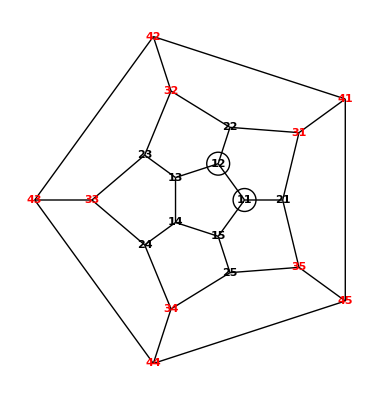

The next figure shows the buttons that are forced to be black by Axiom 1.

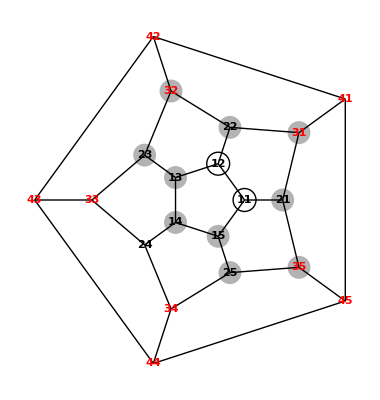

Look to the triples adjacent to the antipodal vertices 35 and 23. By Axiom 2, either 45 or 33 (or both) must be white. Looking similarly to the antipodal vertices 32 and 25 we see that either 42 or 34 (or both) must be white. This I indicate in the next figure:

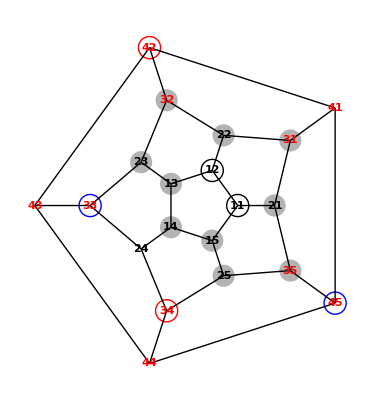

Observe now that 33 and 45 both have 34 and 42 as next-nearest neighbors. If 45 is white then 34 and 42 are necessarily black. But then the antipodal vertices 25 and 42 have only black neighbors, in violation of Axiom 2:

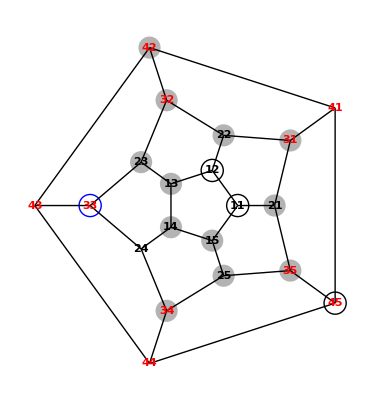

Making 33 white (instead of 45) would have the same  effect, and we are forced to one or the other. Either way, we have a contradiction, and the Lemma is proved.

Completion of Penrose's no-go argument

Assuming without loss of generality that 11 is white, we are forced by the Lemma and Axiom 1 to the configuration shown below:

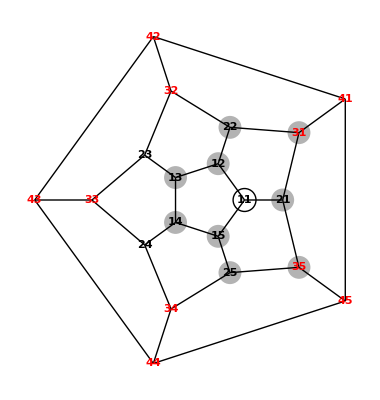

All the buttons adjacent to 11 are black, so one of the buttons adjacent to the antipolar vertex 43 must be white, by Axiom 2. Assume without loss of generality that it is 33.  Lemma and Axiom 1 then enforce the following configuration:

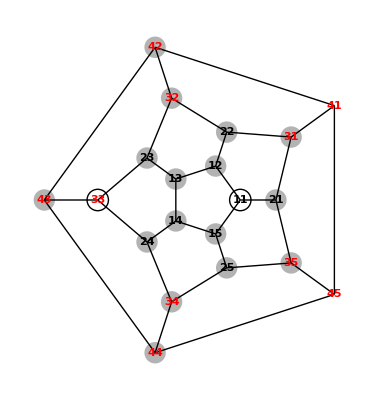

The black vertices adjacent to the antipodal vertices 25 and 32 (ditto 22 and 34) stand now in violation Axiom 2.

We conclude that—quite apart from the difficulties that might arise from coordinating the design of a pair of Quintessential trinkets—our local realist cannot construct even one that conforms to Penrose's quantum mechanically imposed axioms.

Notice, by the way, that while we stipulated at the outset that Quintessential Trinkets are produced in "identical, serial-numbered pairs," our local realist has to assume that they (or the things inside) are non-identical.

### Discussion

Quantum mechanical analysis of the events that can transpire when Alice/Bob play Penrose's game revealed some events that occur statistically (with computable probabilities) and other events that are non-statistical in the sense that they are found never to occur (occur with zero probability). Of course, in every individual game things either happen or they don't—probabilistic/statistical notions become irrelevant. It was from a subset of the events that were found to occur in the quantum mechanical data with zero-probability that Penrose extracted the axioms that must constrain the effort of any local realist to account for the observed facts. 

It was found that the axioms are inconsistent (lead to a contradiction). Note that in arriving at the contradiction we drew upon the Lemma, and that the Lemma is in gross violation of the quantum mechanical facts (facts which by the rules of the game, would never show up in Alice/Bob data). For it is manifestly not the case that ringers cannot be adjacent on a trinket. A single example serves to establish the point:

```mathematica
Chop[A11.A12.singlet]==Subscript[ZeroVector, 16]
```

False

Note also that our local realist, in his failed effort to build a functional trinket, has (see the preceding figure) been obliged to paint so many vertices black (on Alice's trinket, but also—for those same reasons—on Bob's) that it becomes impossible to honor the "poisoned vertex" principle:

```mathematica
Chop[A11.B11.singlet]==Subscript[ZeroVector, 16]
```

True

### Alternative line of argument, more in the tradition of Kochen-Specker

The Bohm-EPR put Alice and Bob to work demonstrating a perfect correlation that arises when make a suitably specialized study of a certain composite system in an entangled state. Perfect correlations are non-statistical, and that particular one invited explanation by a local realist hidden variable theory. That possibility was rendered unfeasible by Bell, who put Alice and Bob to work on a closely related series of experiments that generated statistical evidence of violation of the Bell inequality. Then the Gleason/Bell/Kochen & Specker/Peres/GHZ/Mermin-developments that were addressed to the construction of non-statistical demonstrations that hidden variable theories that embrace the notion of local realism (non-contextual hidden variable theories) cannot account for the quantum mechanical facts. Penrose was inspired by Peres/Kochen-Specker, and by a desire to use only operators of the sort that might be considered to represent measurement devices employed by Alice and Bob (who had not been participants in the developments to which I allude). Preceding discussion has demonstrated his success, but Penrose's main accomplishment actually lies elsewhere.

Early along we were—following Penrose—at pains to identify 40 distinct orthogonal tetrads (20 "natural," 10 "antipodal," 10 "tetrahedral") in the 4-dimensional state space of a spin 3/2particle. But those tetrads played no explicit role in our subsequent work. I turn now to a line of argument for which they were really intended, in which they play the central role. I will be borrowing heavily from "Penrose Dodecahedron: Part III," which was based upon my reading of J. E. Massad & P. K. Avarind, "The Penroise dodecahedron revisited," AJP 67, 631-638 (1999).

To be given a tetrad in 4-space is, in effect, to be given a measurement device which in use invariable projects onto one or another of the elements of that tetrad. Which element is—by the local realist—imagined to be dictated by a hidden "instruction set" secretly written into the design of the state Ψ that device is acting upon. A set of tetrads can be considered to allude to a corresponding set of measurement devices. The imagined "instruction set" must be so detailed that it provides "instructed response" to every such measurement: it must "paint one pre-designated member of each tetrad RED, the other three members BLUE." Penrose used dodecahedral geometry to construct a set of 40 tetrads (all inhabiting the same 4-space) which are interrelated in such a way that inconsistencies afflict every proposed instruction set; every such painting assignment is frustrated. 

I emphasize Alice and Bob have nothing to contribute to this line of argument, which does not depend at all upon experimental data (even the type that provides evidence of perfect correlation), and which involves only a single (not a matched pair of) Quintessential Trinkets.

Here are the 40 tetrads, presented as lists of lists:

```mathematica
Natural1=({{110, 12, 15, 21}, {120, 13, 11, 22}, {130, 14, 12, 23}, {140, 15, 13, 24}, {150, 11, 14, 25}, {210, 11, 35, 31}, {220, 12, 31, 32}, {230, 13, 32, 33}, {240, 14, 33, 34}, {250, 15, 34, 35}})
Natural2=({{430, 44, 42, 33}, {440, 45, 43, 34}, {450, 41, 44, 35}, {410, 42, 45, 31}, {420, 43, 41, 32}, {330, 43, 23, 24}, {340, 44, 24, 25}, {350, 45, 25, 21}, {310, 41, 21, 22}, {320, 42, 22, 23}})
Antipodal=({{11, 110, 43, 430}, {12, 120, 44, 440}, {13, 130, 45, 450}, {14, 140, 41, 410}, {15, 150, 42, 420}, {21, 210, 33, 330}, {22, 220, 34, 340}, {23, 230, 35, 350}, {24, 240, 31, 310}, {25, 250, 32, 320}})
Tetrahedral=({{110, 240, 320, 450}, {110, 230, 340, 410}, {120, 250, 330, 410}, {120, 240, 350, 420}, {130, 210, 340, 420}, {130, 250, 310, 430}, {140, 220, 350, 430}, {140, 210, 320, 440}, {150, 230, 310, 440}, {150, 220, 330, 450}})
```

{{110,12,15,21},{120,13,11,22},{130,14,12,23},{140,15,13,24},{150,11,14,25},{210,11,35,31},{220,12,31,32},{230,13,32,33},{240,14,33,34},{250,15,34,35}}

{{430,44,42,33},{440,45,43,34},{450,41,44,35},{410,42,45,31},{420,43,41,32},{330,43,23,24},{340,44,24,25},{350,45,25,21},{310,41,21,22},{320,42,22,23}}

{{11,110,43,430},{12,120,44,440},{13,130,45,450},{14,140,41,410},{15,150,42,420},{21,210,33,330},{22,220,34,340},{23,230,35,350},{24,240,31,310},{25,250,32,320}}

{{110,240,320,450},{110,230,340,410},{120,250,330,410},{120,240,350,420},{130,210,340,420},{130,250,310,430},{140,220,350,430},{140,210,320,440},{150,230,310,440},{150,220,330,450}}

REMARK: Formerly it was my convention to paint implicit rays red. But Mathematica is computationally color blind. So I use the suffix 0 to distinguish the implicit from the explicit ray at a vertex.

```mathematica
AllTetrads=Union[Natural1, Natural2, Antipodal, Tetrahedral];
Length[AllTetrads]
```

40

```mathematica
AllTetrads
```

{{11,110,43,430},{12,120,44,440},{13,130,45,450},{14,140,41,410},{15,150,42,420},{21,210,33,330},{22,220,34,340},{23,230,35,350},{24,240,31,310},{25,250,32,320},{110,12,15,21},{110,230,340,410},{110,240,320,450},{120,13,11,22},{120,240,350,420},{120,250,330,410},{130,14,12,23},{130,210,340,420},{130,250,310,430},{140,15,13,24},{140,210,320,440},{140,220,350,430},{150,11,14,25},{150,220,330,450},{150,230,310,440},{210,11,35,31},{220,12,31,32},{230,13,32,33},{240,14,33,34},{250,15,34,35},{310,41,21,22},{320,42,22,23},{330,43,23,24},{340,44,24,25},{350,45,25,21},{410,42,45,31},{420,43,41,32},{430,44,42,33},{440,45,43,34},{450,41,44,35}}

I digress now to acquire some list-manipulation tools, and to illustrate how they work:

```mathematica
?Count
?MemberQ
?Position
```

RowBox[{"Count", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["pattern", "TI"]}], "]"}] gives the number of elements in StyleBox["list", "TI"] that match StyleBox["pattern", "TI"]. 
RowBox[{"Count", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] gives the total number of subexpressions matching StyleBox["pattern", "TI"] that appear at the levels in StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"].

RowBox[{"MemberQ", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["form", "TI"]}], "]"}] returns True if an element of StyleBox["list", "TI"] matches StyleBox["form", "TI"], and False otherwise. 
RowBox[{"MemberQ", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["form", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] tests all parts of StyleBox["list", "TI"] specified by StyleBox["levelspec", "TI"].

RowBox[{"Position", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"]}], "]"}] gives a list of the positions at which objects matching StyleBox["pattern", "TI"] appear in StyleBox["expr", "TI"]. 
RowBox[{"Position", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] finds only objects that appear on levels specified by StyleBox["levelspec", "TI"]. 
RowBox[{"Position", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the positions of the first StyleBox["n", "TI"] objects found.

```mathematica
Count[AllTetrads, {440,45,43,34}]
MemberQ[AllTetrads, {440,45,43,34}]
Position[AllTetrads, {440,45,43,34}]
```

1

True

{{39}}

```mathematica
AllTetrads⟦39⟧
```

{440,45,43,34}

If you had 40 workers from which to select teams of 4 to solve 40 tasks you would expect each worker to serve on 4 teams. In view of the symmetry of the dodecahedron one, by similar reasoning, expects each ray (whether explicit or implicit) to be a member of four tetrads. And indeed, if we look serially to all tetrads, asking whether some given ray is a member, and counting the number of True responses, we in every case get 4: thus

```mathematica
Table[{n,MemberQ[AllTetrads⟦n⟧,11]}, {n,1,40}]
```

{{1,True},{2,False},{3,False},{4,False},{5,False},{6,False},{7,False},{8,False},{9,False},{10,False},{11,False},{12,False},{13,False},{14,True},{15,False},{16,False},{17,False},{18,False},{19,False},{20,False},{21,False},{22,False},{23,True},{24,False},{25,False},{26,True},{27,False},{28,False},{29,False},{30,False},{31,False},{32,False},{33,False},{34,False},{35,False},{36,False},{37,False},{38,False},{39,False},{40,False}}

```mathematica
∑_(k=1)^40 Count[%,{k,True}]
```

4

Suppose that—arbitrarily—we elect to paint the 11-ray RED. All rays orthogonal to 11 —which is to say: all the rays in the four tetrads that include 11 as a member—have then to be painted BLUE.

```mathematica
Table[{n,MemberQ[AllTetrads⟦n⟧,11]}, {n,1,40}]//TableForm
```

1 | True
2 | False
3 | False
4 | False
5 | False
6 | False
7 | False
8 | False
9 | False
10 | False
11 | False
12 | False
13 | False
14 | True
15 | False
16 | False
17 | False
18 | False
19 | False
20 | False
21 | False
22 | False
23 | True
24 | False
25 | False
26 | True
27 | False
28 | False
29 | False
30 | False
31 | False
32 | False
33 | False
34 | False
35 | False
36 | False
37 | False
38 | False
39 | False
40 | False

```mathematica
AllTetrads⟦1⟧
AllTetrads⟦14⟧
AllTetrads⟦23⟧
AllTetrads⟦26⟧
```

{11,110,43,430}

{120,13,11,22}

{150,11,14,25}

{210,11,35,31}

```mathematica
Union[%,%%,%%%,%%%%]
```

{11,13,14,22,25,31,35,43,110,120,150,210,430}

The last twelve of those are orthogonal to 11, so have to be painted BLUE:

```mathematica
FirstReduction=AllTetrads/.{13->0,14->0,22->0,25->0,31->0,35->0,43->0,110->0,120->0,150->0,210->0,430->0}
```

{{11,0,0,0},{12,0,44,440},{0,130,45,450},{0,140,41,410},{15,0,42,420},{21,0,33,330},{0,220,34,340},{23,230,0,350},{24,240,0,310},{0,250,32,320},{0,12,15,21},{0,230,340,410},{0,240,320,450},{0,0,11,0},{0,240,350,420},{0,250,330,410},{130,0,12,23},{130,0,340,420},{130,250,310,0},{140,15,0,24},{140,0,320,440},{140,220,350,0},{0,11,0,0},{0,220,330,450},{0,230,310,440},{0,11,0,0},{220,12,0,32},{230,0,32,33},{240,0,33,34},{250,15,34,0},{310,41,21,0},{320,42,0,23},{330,0,23,24},{340,44,24,0},{350,45,0,21},{410,42,45,0},{420,0,41,32},{0,44,42,33},{440,45,0,34},{450,41,44,0}}

12 is a survivor on the list; paint it also RED.

```mathematica
Table[{n,MemberQ[FirstReduction⟦n⟧,12]}, {n,1,40}]//TableForm
```

1 | False
2 | True
3 | False
4 | False
5 | False
6 | False
7 | False
8 | False
9 | False
10 | False
11 | True
12 | False
13 | False
14 | False
15 | False
16 | False
17 | True
18 | False
19 | False
20 | False
21 | False
22 | False
23 | False
24 | False
25 | False
26 | False
27 | True
28 | False
29 | False
30 | False
31 | False
32 | False
33 | False
34 | False
35 | False
36 | False
37 | False
38 | False
39 | False
40 | False

```mathematica
FirstReduction⟦2⟧
FirstReduction⟦11⟧
FirstReduction⟦17⟧
FirstReduction⟦27⟧
```

{12,0,44,440}

{0,12,15,21}

{130,0,12,23}

{220,12,0,32}

We have now an additional population of rays that must be painted BLUE:

```mathematica
Union[%,%%,%%%,%%%%]
```

{0,12,15,21,23,32,44,130,220,440}

```mathematica
SecondReduction=FirstReduction/.{15->0,21->0,23->0,32->0,44->0,130->0,220->0,440->0}
```

{{11,0,0,0},{12,0,0,0},{0,0,45,450},{0,140,41,410},{0,0,42,420},{0,0,33,330},{0,0,34,340},{0,230,0,350},{24,240,0,310},{0,250,0,320},{0,12,0,0},{0,230,340,410},{0,240,320,450},{0,0,11,0},{0,240,350,420},{0,250,330,410},{0,0,12,0},{0,0,340,420},{0,250,310,0},{140,0,0,24},{140,0,320,0},{140,0,350,0},{0,11,0,0},{0,0,330,450},{0,230,310,0},{0,11,0,0},{0,12,0,0},{230,0,0,33},{240,0,33,34},{250,0,34,0},{310,41,0,0},{320,42,0,0},{330,0,0,24},{340,0,24,0},{350,45,0,0},{410,42,45,0},{420,0,41,0},{0,0,42,33},{0,45,0,34},{450,41,0,0}}

45 is the next survivor on the list. We paint it RED:

```mathematica
Table[{n,MemberQ[SecondReduction⟦n⟧,45]}, {n,1,40}]//TableForm
```

1 | False
2 | False
3 | True
4 | False
5 | False
6 | False
7 | False
8 | False
9 | False
10 | False
11 | False
12 | False
13 | False
14 | False
15 | False
16 | False
17 | False
18 | False
19 | False
20 | False
21 | False
22 | False
23 | False
24 | False
25 | False
26 | False
27 | False
28 | False
29 | False
30 | False
31 | False
32 | False
33 | False
34 | False
35 | True
36 | True
37 | False
38 | False
39 | True
40 | False

```mathematica
SecondReduction⟦3⟧
SecondReduction⟦35⟧
SecondReduction⟦36⟧
SecondReduction⟦39⟧
```

{0,0,45,450}

{350,45,0,0}

{410,42,45,0}

{0,45,0,34}

We have now still more rays to paint BLUE:

```mathematica
Union[%,%%,%%%,%%%%]
```

{0,34,42,45,350,410,450}

```mathematica
ThirdReduction=SecondReduction/.{34->0,42->0,350->0,410->0,450->0}
```

{{11,0,0,0},{12,0,0,0},{0,0,45,0},{0,140,41,0},{0,0,0,420},{0,0,33,330},{0,0,0,340},{0,230,0,0},{24,240,0,310},{0,250,0,320},{0,12,0,0},{0,230,340,0},{0,240,320,0},{0,0,11,0},{0,240,0,420},{0,250,330,0},{0,0,12,0},{0,0,340,420},{0,250,310,0},{140,0,0,24},{140,0,320,0},{140,0,0,0},{0,11,0,0},{0,0,330,0},{0,230,310,0},{0,11,0,0},{0,12,0,0},{230,0,0,33},{240,0,33,0},{250,0,0,0},{310,41,0,0},{320,0,0,0},{330,0,0,24},{340,0,24,0},{0,45,0,0},{0,0,45,0},{420,0,41,0},{0,0,0,33},{0,45,0,0},{0,41,0,0}}

140 is the next survivor. We paint it RED :

```mathematica
Table[{n,MemberQ[ThirdReduction⟦n⟧,140]}, {n,1,40}]//TableForm
```

1 | False
2 | False
3 | False
4 | True
5 | False
6 | False
7 | False
8 | False
9 | False
10 | False
11 | False
12 | False
13 | False
14 | False
15 | False
16 | False
17 | False
18 | False
19 | False
20 | True
21 | True
22 | True
23 | False
24 | False
25 | False
26 | False
27 | False
28 | False
29 | False
30 | False
31 | False
32 | False
33 | False
34 | False
35 | False
36 | False
37 | False
38 | False
39 | False
40 | False

```mathematica
ThirdReduction⟦4⟧
ThirdReduction⟦20⟧
ThirdReduction⟦21⟧
ThirdReduction⟦22⟧
```

{0,140,41,0}

{140,0,0,24}

{140,0,320,0}

{140,0,0,0}

Now also these must be painted BLUE:

```mathematica
Union[%,%%,%%%,%%%%]
```

{0,24,41,140,320}

```mathematica
FourthReduction=ThirdReduction/.{24->0,41->0,320->0}
```

{{11,0,0,0},{12,0,0,0},{0,0,45,0},{0,140,0,0},{0,0,0,420},{0,0,33,330},{0,0,0,340},{0,230,0,0},{0,240,0,310},{0,250,0,0},{0,12,0,0},{0,230,340,0},{0,240,0,0},{0,0,11,0},{0,240,0,420},{0,250,330,0},{0,0,12,0},{0,0,340,420},{0,250,310,0},{140,0,0,0},{140,0,0,0},{140,0,0,0},{0,11,0,0},{0,0,330,0},{0,230,310,0},{0,11,0,0},{0,12,0,0},{230,0,0,33},{240,0,33,0},{250,0,0,0},{310,0,0,0},{0,0,0,0},{330,0,0,0},{340,0,0,0},{0,45,0,0},{0,0,45,0},{420,0,0,0},{0,0,0,33},{0,45,0,0},{0,0,0,0}}

We notice that

```mathematica
Count[FourthReduction,{0,0,0,0}]
```

2

of the tetrads have been forced to become ENTIRELY BLUE: THEY CONTAIN NO ROOM FOR THE MANDATORY RED RAY. This completes the uncolorability proof (or would if we could convince ourselves that the arbitrary choices we made along the way, if replaced by any other set of arbitrary choices, would lead to a similar result) and establishes Penrose's no-go theorem.

Let us nevertheless carry the argument forward as far as we can. 33 is the next survivor. We paint it RED and notice that now all the surviving rays have been painted RED:

```mathematica
Table[{n,MemberQ[FourthReduction⟦n⟧,33]}, {n,1,40}]//TableForm
```

1 | False
2 | False
3 | False
4 | False
5 | False
6 | True
7 | False
8 | False
9 | False
10 | False
11 | False
12 | False
13 | False
14 | False
15 | False
16 | False
17 | False
18 | False
19 | False
20 | False
21 | False
22 | False
23 | False
24 | False
25 | False
26 | False
27 | False
28 | True
29 | True
30 | False
31 | False
32 | False
33 | False
34 | False
35 | False
36 | False
37 | False
38 | True
39 | False
40 | False

```mathematica
FourthReduction⟦6⟧
FourthReduction⟦28⟧
FourthReduction⟦29⟧
FourthReduction⟦38⟧
```

{0,0,33,330}

{230,0,0,33}

{240,0,33,0}

{0,0,0,33}

```mathematica
Union[%,%%,%%%,%%%%]
```

{0,33,230,240,330}

```mathematica
FifthReduction=FourthReduction/.{230->0,240->0,330->0}
```

{{11,0,0,0},{12,0,0,0},{0,0,45,0},{0,140,0,0},{0,0,0,420},{0,0,33,0},{0,0,0,340},{0,0,0,0},{0,0,0,310},{0,250,0,0},{0,12,0,0},{0,0,340,0},{0,0,0,0},{0,0,11,0},{0,0,0,420},{0,250,0,0},{0,0,12,0},{0,0,340,420},{0,250,310,0},{140,0,0,0},{140,0,0,0},{140,0,0,0},{0,11,0,0},{0,0,0,0},{0,0,310,0},{0,11,0,0},{0,12,0,0},{0,0,0,33},{0,0,33,0},{250,0,0,0},{310,0,0,0},{0,0,0,0},{0,0,0,0},{340,0,0,0},{0,45,0,0},{0,0,45,0},{0,0,0,0},{0,0,0,33},{0,45,0,0},{0,0,0,0}}

340 is the next survivor. Paint it RED.

```mathematica
Table[{n,MemberQ[FifthReduction⟦n⟧,340]}, {n,1,40}]//TableForm
```

1 | False
2 | False
3 | False
4 | False
5 | False
6 | False
7 | True
8 | False
9 | False
10 | False
11 | False
12 | True
13 | False
14 | False
15 | False
16 | False
17 | False
18 | True
19 | False
20 | False
21 | False
22 | False
23 | False
24 | False
25 | False
26 | False
27 | False
28 | False
29 | False
30 | False
31 | False
32 | False
33 | False
34 | True
35 | False
36 | False
37 | False
38 | False
39 | False
40 | False

```mathematica
FifthReduction⟦7⟧
FifthReduction⟦12⟧
FifthReduction⟦18⟧
FifthReduction⟦34⟧
```

{0,0,0,340}

{0,0,340,0}

{0,0,340,420}

{340,0,0,0}

```mathematica
Union[%,%%,%%%,%%%%]
```

{0,340,420}

We are forced to paint 420 BLUE, which leaves us with

```mathematica
SixthReduction=FifthReduction/.{420->0}
```

{{11,0,0,0},{12,0,0,0},{0,0,45,0},{0,140,0,0},{0,0,0,0},{0,0,33,0},{0,0,0,340},{0,0,0,0},{0,0,0,310},{0,250,0,0},{0,12,0,0},{0,0,340,0},{0,0,0,0},{0,0,11,0},{0,0,0,0},{0,250,0,0},{0,0,12,0},{0,0,340,0},{0,250,310,0},{140,0,0,0},{140,0,0,0},{140,0,0,0},{0,11,0,0},{0,0,0,0},{0,0,310,0},{0,11,0,0},{0,12,0,0},{0,0,0,33},{0,0,33,0},{250,0,0,0},{310,0,0,0},{0,0,0,0},{0,0,0,0},{340,0,0,0},{0,45,0,0},{0,0,45,0},{0,0,0,0},{0,0,0,33},{0,45,0,0},{0,0,0,0}}

Finally we paint 250 RED:

```mathematica
Table[{n,MemberQ[FifthReduction⟦n⟧,250]}, {n,1,40}]//TableForm
```

1 | False
2 | False
3 | False
4 | False
5 | False
6 | False
7 | False
8 | False
9 | False
10 | True
11 | False
12 | False
13 | False
14 | False
15 | False
16 | True
17 | False
18 | False
19 | True
20 | False
21 | False
22 | False
23 | False
24 | False
25 | False
26 | False
27 | False
28 | False
29 | False
30 | True
31 | False
32 | False
33 | False
34 | False
35 | False
36 | False
37 | False
38 | False
39 | False
40 | False

```mathematica
SixthReduction⟦10⟧
SixthReduction⟦16⟧
SixthReduction⟦19⟧
SixthReduction⟦30⟧
```

{0,250,0,0}

{0,250,0,0}

{0,250,310,0}

{250,0,0,0}

```mathematica
Union[%,%%,%%%,%%%%]
```

{0,250,310}

We are now forced to paint 310 BLUE, which leaves us with

```mathematica
SeventhReduction=SixthReduction/.{310->0}
```

{{11,0,0,0},{12,0,0,0},{0,0,45,0},{0,140,0,0},{0,0,0,0},{0,0,33,0},{0,0,0,340},{0,0,0,0},{0,0,0,0},{0,250,0,0},{0,12,0,0},{0,0,340,0},{0,0,0,0},{0,0,11,0},{0,0,0,0},{0,250,0,0},{0,0,12,0},{0,0,340,0},{0,250,0,0},{140,0,0,0},{140,0,0,0},{140,0,0,0},{0,11,0,0},{0,0,0,0},{0,0,0,0},{0,11,0,0},{0,12,0,0},{0,0,0,33},{0,0,33,0},{250,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{340,0,0,0},{0,45,0,0},{0,0,45,0},{0,0,0,0},{0,0,0,33},{0,45,0,0},{0,0,0,0}}

This list contains

```mathematica
Count[%,{0,0,0,0}]
```

12

ALL-BLUE TETRADS, and 28 that do in fact contain the mandatory SINGLE RED RAY AND THREE BLUE RAYS. Our ray-painting project has come to its end.

When we look to the tetrads that our arbitrarily-selected sequence {11, 12, 45, 33, 140, 340, 250} of red rays forced to be all blue

```mathematica
Table[{n,{SeventhReduction⟦n⟧}},{n,1,40}]//TableForm
```

1 | 11 | 0 | 0 | 0
2 | 12 | 0 | 0 | 0
3 | 0 | 0 | 45 | 0
4 | 0 | 140 | 0 | 0
5 | 0 | 0 | 0 | 0
6 | 0 | 0 | 33 | 0
7 | 0 | 0 | 0 | 340
8 | 0 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0
10 | 0 | 250 | 0 | 0
11 | 0 | 12 | 0 | 0
12 | 0 | 0 | 340 | 0
13 | 0 | 0 | 0 | 0
14 | 0 | 0 | 11 | 0
15 | 0 | 0 | 0 | 0
16 | 0 | 250 | 0 | 0
17 | 0 | 0 | 12 | 0
18 | 0 | 0 | 340 | 0
19 | 0 | 250 | 0 | 0
20 | 140 | 0 | 0 | 0
21 | 140 | 0 | 0 | 0
22 | 140 | 0 | 0 | 0
23 | 0 | 11 | 0 | 0
24 | 0 | 0 | 0 | 0
25 | 0 | 0 | 0 | 0
26 | 0 | 11 | 0 | 0
27 | 0 | 12 | 0 | 0
28 | 0 | 0 | 0 | 33
29 | 0 | 0 | 33 | 0
30 | 250 | 0 | 0 | 0
31 | 0 | 0 | 0 | 0
32 | 0 | 0 | 0 | 0
33 | 0 | 0 | 0 | 0
34 | 340 | 0 | 0 | 0
35 | 0 | 45 | 0 | 0
36 | 0 | 0 | 45 | 0
37 | 0 | 0 | 0 | 0
38 | 0 | 0 | 0 | 33
39 | 0 | 45 | 0 | 0
40 | 0 | 0 | 0 | 0

we find that they comprise 3 antipodal tetrads

```mathematica
AllTetrads⟦5⟧
AllTetrads⟦8⟧
AllTetrads⟦9⟧
```

{15,150,42,420}

{23,230,35,350}

{24,240,31,310}

4 tetrahedral tetrads

```mathematica
AllTetrads⟦13⟧
AllTetrads⟦15⟧
AllTetrads⟦24⟧
AllTetrads⟦25⟧
```

{110,240,320,450}

{120,240,350,420}

{150,220,330,450}

{150,230,310,440}

and five natural tetrads:

```mathematica
AllTetrads⟦31⟧
AllTetrads⟦32⟧
AllTetrads⟦33⟧
AllTetrads⟦37⟧
AllTetrads⟦40⟧
```

{310,41,21,22}

{320,42,22,23}

{330,43,23,24}

{430,43,41,32}

{450,41,44,35}

But I do not know what significance to attach to this fact, which I suspect is not at all deep or interesting.

My simple objective, at each step in the preceding calculations, has been to 
    • identify all the tetrads that contain an arbitrarily selected ray;
    • identify, in those tetrads, all the (orthogonal) companions of the selected ray;
    • eliminate (meaning "paint blue") those rays wherever they appear in the complete list of 40 tetrads.
The means I have devised to employ Mathematica to accomplish that objective is clumsy, but I have not been able to discover the list-manipulation resources that would be required to make the procedure more efficient.  On 26 March 2007 I approached Joel Franklin to see whether he might be able to "automate" the precedure illustrated above. Within 20 minutes he had produced the following bit of Mathematica programing:

```mathematica
GetSymbols[alltets_] := Module[{symbollist,uniquelist,index},
symbollist = Sort[Flatten[alltets]];
symbollist = Select[symbollist, #=!= 0 &];
uniquelist = {symbollist[[1]]};
For[index = 2, index ≤ Length[symbollist], index++,
If[symbollist[[index]]  =!= symbollist[[index-1]] && symbollist[[index]] =!= 0,
uniquelist = Join[uniquelist, {symbollist[[index]]}];
];
];
uniquelist
]
```

```mathematica
IsIn[inlist_, insym_] := If[Length[Select[inlist, # == insym&]] == 1, True,False]
```

```mathematica
ColorSymbol[tetlist_, symbolname_] := Module[{slist, inlist, reptable},
inlist = Select[tetlist, IsIn[#,symbolname]&];
Print[symbolname," Appears in :: ",inlist];
inlist = Flatten[inlist];
inlist = Select[inlist,#=!= symbolname&];
Print["I am setting the following to zero :: ",inlist];
reptable = Table[inlist[[jj]] -> 0,{jj,1,Length[inlist]}];
tetlist //.reptable
]
```

```mathematica
AllNotIn[biglist_, exciselist_] := Module[{olist,index},
olist = {};
For[index = 1, index ≤ Length[biglist], index++,
If[IsIn[exciselist, biglist[[index]]] == False, olist = Join[olist,{biglist[[index]]}]];
];
olist
]
```

```mathematica
ColorAll[tetlist_] := Module[{ltets, olist, done,slist,symbol, usedsymbols},
done = False;
slist = GetSymbols[tetlist];
symbol = slist[[1]];
usedsymbols = {};
ltets = tetlist;
While[done == False,
ltets = ColorSymbol[ltets, symbol];
slist = GetSymbols[ltets];
usedsymbols = Join[usedsymbols, {symbol}];
 slist = AllNotIn[slist, usedsymbols];
If[Length[slist]  == 0,done = True;, symbol = slist[[1]]];
];
ltets
]
```

I show how Joel's program is used to reproduce with only a few keystrokes the results I labored so patiently to obtained:

```mathematica
ltets = ColorSymbol[AllTetrads, 11]
```

11 Appears in :: {{11,110,43,430},{120,13,11,22},{150,11,14,25},{210,11,35,31}}

I am setting the following to zero :: {110,43,430,120,13,22,150,14,25,210,35,31}

{{11,0,0,0},{12,0,44,440},{0,130,45,450},{0,140,41,410},{15,0,42,420},{21,0,33,330},{0,220,34,340},{23,230,0,350},{24,240,0,310},{0,250,32,320},{0,12,15,21},{0,230,340,410},{0,240,320,450},{0,0,11,0},{0,240,350,420},{0,250,330,410},{130,0,12,23},{130,0,340,420},{130,250,310,0},{140,15,0,24},{140,0,320,440},{140,220,350,0},{0,11,0,0},{0,220,330,450},{0,230,310,440},{0,11,0,0},{220,12,0,32},{230,0,32,33},{240,0,33,34},{250,15,34,0},{310,41,21,0},{320,42,0,23},{330,0,23,24},{340,44,24,0},{350,45,0,21},{410,42,45,0},{0,0,41,32},{0,44,42,33},{440,45,0,34},{450,41,44,0}}

```mathematica
ltets = ColorSymbol[ltets, 12]
```

12 Appears in :: {{12,0,44,440},{0,12,15,21},{130,0,12,23},{220,12,0,32}}

I am setting the following to zero :: {0,44,440,0,15,21,130,0,23,220,0,32}

{{11,0,0,0},{12,0,0,0},{0,0,45,450},{0,140,41,410},{0,0,42,420},{0,0,33,330},{0,0,34,340},{0,230,0,350},{24,240,0,310},{0,250,0,320},{0,12,0,0},{0,230,340,410},{0,240,320,450},{0,0,11,0},{0,240,350,420},{0,250,330,410},{0,0,12,0},{0,0,340,420},{0,250,310,0},{140,0,0,24},{140,0,320,0},{140,0,350,0},{0,11,0,0},{0,0,330,450},{0,230,310,0},{0,11,0,0},{0,12,0,0},{230,0,0,33},{240,0,33,34},{250,0,34,0},{310,41,0,0},{320,42,0,0},{330,0,0,24},{340,0,24,0},{350,45,0,0},{410,42,45,0},{0,0,41,0},{0,0,42,33},{0,45,0,34},{450,41,0,0}}

```mathematica
ltets = ColorSymbol[ltets, 45]
```

45 Appears in :: {{0,0,45,450},{350,45,0,0},{410,42,45,0},{0,45,0,34}}

I am setting the following to zero :: {0,0,450,350,0,0,410,42,0,0,0,34}

{{11,0,0,0},{12,0,0,0},{0,0,45,0},{0,140,41,0},{0,0,0,420},{0,0,33,330},{0,0,0,340},{0,230,0,0},{24,240,0,310},{0,250,0,320},{0,12,0,0},{0,230,340,0},{0,240,320,0},{0,0,11,0},{0,240,0,420},{0,250,330,0},{0,0,12,0},{0,0,340,420},{0,250,310,0},{140,0,0,24},{140,0,320,0},{140,0,0,0},{0,11,0,0},{0,0,330,0},{0,230,310,0},{0,11,0,0},{0,12,0,0},{230,0,0,33},{240,0,33,0},{250,0,0,0},{310,41,0,0},{320,0,0,0},{330,0,0,24},{340,0,24,0},{0,45,0,0},{0,0,45,0},{0,0,41,0},{0,0,0,33},{0,45,0,0},{0,41,0,0}}

```mathematica
ltets = ColorSymbol[ltets, 140]
```

140 Appears in :: {{0,140,41,0},{140,0,0,24},{140,0,320,0},{140,0,0,0}}

I am setting the following to zero :: {0,41,0,0,0,24,0,320,0,0,0,0}

{{11,0,0,0},{12,0,0,0},{0,0,45,0},{0,140,0,0},{0,0,0,420},{0,0,33,330},{0,0,0,340},{0,230,0,0},{0,240,0,310},{0,250,0,0},{0,12,0,0},{0,230,340,0},{0,240,0,0},{0,0,11,0},{0,240,0,420},{0,250,330,0},{0,0,12,0},{0,0,340,420},{0,250,310,0},{140,0,0,0},{140,0,0,0},{140,0,0,0},{0,11,0,0},{0,0,330,0},{0,230,310,0},{0,11,0,0},{0,12,0,0},{230,0,0,33},{240,0,33,0},{250,0,0,0},{310,0,0,0},{0,0,0,0},{330,0,0,0},{340,0,0,0},{0,45,0,0},{0,0,45,0},{0,0,0,0},{0,0,0,33},{0,45,0,0},{0,0,0,0}}

```mathematica
Count[%, {0,0,0,0}]
```

3

```mathematica
ltets = ColorSymbol[ltets, 140]
```

140 Appears in :: {{0,140,41,0},{140,0,0,24},{140,0,320,0},{140,0,0,0}}

I am setting the following to zero :: {0,41,0,0,0,24,0,320,0,0,0,0}

{{11,0,0,0},{12,0,0,0},{0,0,45,0},{0,140,0,0},{0,0,0,420},{0,0,33,0},{0,0,0,340},{0,0,0,0},{0,0,0,310},{0,250,0,0},{0,12,0,0},{0,0,340,0},{0,0,0,0},{0,0,11,0},{0,0,0,420},{0,250,0,0},{0,0,12,0},{0,0,340,420},{0,250,310,0},{140,0,0,0},{140,0,0,0},{140,0,0,0},{0,11,0,0},{0,0,0,0},{0,0,310,0},{0,11,0,0},{0,12,0,0},{0,0,0,33},{0,0,33,0},{250,0,0,0},{310,0,0,0},{0,0,0,0},{0,0,0,0},{340,0,0,0},{0,45,0,0},{0,0,45,0},{0,0,0,0},{0,0,0,33},{0,45,0,0},{0,0,0,0}}

```mathematica
ltets = ColorSymbol[ltets, 340]
```

340 Appears in :: {{0,0,0,340},{0,0,340,0},{0,0,340,420},{340,0,0,0}}

I am setting the following to zero :: {0,0,0,0,0,0,0,0,420,0,0,0}

{{11,0,0,0},{12,0,0,0},{0,0,45,0},{0,140,0,0},{0,0,0,0},{0,0,33,0},{0,0,0,340},{0,0,0,0},{0,0,0,310},{0,250,0,0},{0,12,0,0},{0,0,340,0},{0,0,0,0},{0,0,11,0},{0,0,0,0},{0,250,0,0},{0,0,12,0},{0,0,340,0},{0,250,310,0},{140,0,0,0},{140,0,0,0},{140,0,0,0},{0,11,0,0},{0,0,0,0},{0,0,310,0},{0,11,0,0},{0,12,0,0},{0,0,0,33},{0,0,33,0},{250,0,0,0},{310,0,0,0},{0,0,0,0},{0,0,0,0},{340,0,0,0},{0,45,0,0},{0,0,45,0},{0,0,0,0},{0,0,0,33},{0,45,0,0},{0,0,0,0}}

```mathematica
ltets = ColorSymbol[ltets, 250]
```

250 Appears in :: {{0,250,0,0},{0,250,0,0},{0,250,310,0},{250,0,0,0}}

I am setting the following to zero :: {0,0,0,0,0,0,0,310,0,0,0,0}

{{11,0,0,0},{12,0,0,0},{0,0,45,0},{0,140,0,0},{0,0,0,0},{0,0,33,0},{0,0,0,340},{0,0,0,0},{0,0,0,0},{0,250,0,0},{0,12,0,0},{0,0,340,0},{0,0,0,0},{0,0,11,0},{0,0,0,0},{0,250,0,0},{0,0,12,0},{0,0,340,0},{0,250,0,0},{140,0,0,0},{140,0,0,0},{140,0,0,0},{0,11,0,0},{0,0,0,0},{0,0,0,0},{0,11,0,0},{0,12,0,0},{0,0,0,33},{0,0,33,0},{250,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{340,0,0,0},{0,45,0,0},{0,0,45,0},{0,0,0,0},{0,0,0,33},{0,45,0,0},{0,0,0,0}}

```mathematica
Count[%,{0,0,0,0}]
```

12

### Penrose's abbreviated list of uncolorable rays

Near the end of their paper, Massad & Aravind draw attention to the fact—first pointed out by Zimba & Penrose—that if one abandons all implicit rays except those associated with the vertices of one of the (five) inscribed cubes one obtains an uncolorable set of (not 40 but only) 28 rays. My objective here is  to check the accuracy of that claim.

Here is a list of the implicit rays associated with the 8 vertices of one of the two cubes that contain 11 as a  vertex:

```mathematica
{110,140,220,230,350,340,410,430}
```

The implicit rays to be eliminated are therefore

```mathematica
Complement[{110,120,130,140,150,210,220,230,240,250,310,320,330,340,350,410,420,430,440,450},{110,140,220,230,350,340,410,430}]
```

{120,130,150,210,240,250,310,320,330,420,440,450}

To eliminate all the tetrads that contain on or another (or several) of thos implicit rays we proceed via

```mathematica
AllTetrads/.{120->0,140->0,150->0,210->0,220->0,230->0,330->0,340->0,350->0,410->0,420->0,440->0}
```

{{11,110,43,430},{12,0,44,0},{13,130,45,450},{14,0,41,0},{15,0,42,0},{21,0,33,0},{22,0,34,0},{23,0,35,0},{24,240,31,310},{25,250,32,320},{110,12,15,21},{110,0,0,0},{110,240,320,450},{0,13,11,22},{0,240,0,0},{0,250,0,0},{130,14,12,23},{130,0,0,0},{130,250,310,430},{0,15,13,24},{0,0,320,0},{0,0,0,430},{0,11,14,25},{0,0,0,450},{0,0,310,0},{0,11,35,31},{0,12,31,32},{0,13,32,33},{240,14,33,34},{250,15,34,35},{310,41,21,22},{320,42,22,23},{0,43,23,24},{0,44,24,25},{0,45,25,21},{0,42,45,31},{0,43,41,32},{430,44,42,33},{0,45,43,34},{450,41,44,35}}

to a

```mathematica
ShortList={{11,110,43,430},{14,140,41,410},{22,220,34,340},{23,230,35,350},{110,12,15,21},{110,230,340,410},{140,15,13,24},{140,220,350,430},{220,12,31,32},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}};
```

made of (not 40, but)  only

```mathematica
Length[ShortList]
```

14

tetrads. I demonstrate that this short list is uncolorable:

```mathematica
ltets = ColorSymbol[ShortList, 11]
```

11 Appears in :: {{11,110,43,430}}

I am setting the following to zero :: {110,43,430}

{{11,0,0,0},{14,140,41,410},{22,220,34,340},{23,230,35,350},{0,12,15,21},{0,230,340,410},{140,15,13,24},{140,220,350,0},{220,12,31,32},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{0,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets, 21]
```

21 Appears in :: {{0,12,15,21},{350,45,25,21}}

I am setting the following to zero :: {0,12,15,350,45,25}

{{11,0,0,0},{14,140,41,410},{22,220,34,340},{23,230,35,0},{0,0,0,21},{0,230,340,410},{140,0,13,24},{140,220,0,0},{220,0,31,32},{230,13,32,33},{340,44,24,0},{0,0,0,21},{410,42,0,31},{0,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets,32]
```

32 Appears in :: {{220,0,31,32},{230,13,32,33}}

I am setting the following to zero :: {220,0,31,230,13,33}

{{11,0,0,0},{14,140,41,410},{22,0,34,340},{23,0,35,0},{0,0,0,21},{0,0,340,410},{140,0,0,24},{140,0,0,0},{0,0,0,32},{0,0,32,0},{340,44,24,0},{0,0,0,21},{410,42,0,0},{0,44,42,0}}

```mathematica
ltets = ColorSymbol[ltets, 23]
```

23 Appears in :: {{23,0,35,0}}

I am setting the following to zero :: {0,35,0}

{{11,0,0,0},{14,140,41,410},{22,0,34,340},{23,0,0,0},{0,0,0,21},{0,0,340,410},{140,0,0,24},{140,0,0,0},{0,0,0,32},{0,0,32,0},{340,44,24,0},{0,0,0,21},{410,42,0,0},{0,44,42,0}}

```mathematica
ltets = ColorSymbol[ltets,140]
```

140 Appears in :: {{14,140,41,410},{140,0,0,24},{140,0,0,0}}

I am setting the following to zero :: {14,41,410,0,0,24,0,0,0}

{{11,0,0,0},{0,140,0,0},{22,0,34,340},{23,0,0,0},{0,0,0,21},{0,0,340,0},{140,0,0,0},{140,0,0,0},{0,0,0,32},{0,0,32,0},{340,44,0,0},{0,0,0,21},{0,42,0,0},{0,44,42,0}}

```mathematica
ltets = ColorSymbol[ltets,34]
```

34 Appears in :: {{22,0,34,340}}

I am setting the following to zero :: {22,0,340}

{{11,0,0,0},{0,140,0,0},{0,0,34,0},{23,0,0,0},{0,0,0,21},{0,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,0,32},{0,0,32,0},{0,44,0,0},{0,0,0,21},{0,42,0,0},{0,44,42,0}}

```mathematica
ltets = ColorSymbol[ltets,42]
```

42 Appears in :: {{0,42,0,0},{0,44,42,0}}

I am setting the following to zero :: {0,0,0,0,44,0}

{{11,0,0,0},{0,140,0,0},{0,0,34,0},{23,0,0,0},{0,0,0,21},{0,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,0,32},{0,0,32,0},{0,0,0,0},{0,0,0,21},{0,42,0,0},{0,0,42,0}}

```mathematica
Count[%,{0,0,0,0}]
```

2

Uncolorability is established.

REMARK: I painted rays red in this sequence {11, 21, 32, 23, 140, 34, 42} in order to follow in the notationally adjusted footsteps of "Penrose Dodecahedron: Part III." I follow in those footsteps as a way of guarding against the translational errors that have dogged me this afternoon. In the course of that work I have discovered that what emerges from Joel's algorithm as the "most natural" sequence establishes uncolorability in only four moves.

### Restoration of colorability

Massad & Aravind have drawn attention to Zimba/Penrose's observation that deletion of a single ray from their abbreviated list is sufficient to make colorability possible, and thus establish a sense in which their abbreviated list is smallest-possible. To establish the point, we must distinguish three possibilities:
    • an implicit ray at a cubic vertex;
    • an explicit ray at a cubic vertex;
    • an explicit ray not at a cubic vertex.
I look to those cases one at a time, in the sequence stated:

-Graphics3D-

```mathematica
ShortList
```

{{11,110,43,430},{14,140,41,410},{22,220,34,340},{23,230,35,350},{110,12,15,21},{110,230,340,410},{140,15,13,24},{140,220,350,430},{220,12,31,32},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}}

```mathematica
Length[ShortList]
```

14

```mathematica
ShortList/.{110->0}
```

{{11,0,43,430},{14,140,41,410},{22,220,34,340},{23,230,35,350},{0,12,15,21},{0,230,340,410},{140,15,13,24},{140,220,350,430},{220,12,31,32},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}}

```mathematica
ShorterList1={{14,140,41,410},{22,220,34,340},{23,230,35,350},{140,15,13,24},{140,220,350,430},{220,12,31,32},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}}
```

{{14,140,41,410},{22,220,34,340},{23,230,35,350},{140,15,13,24},{140,220,350,430},{220,12,31,32},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}}

```mathematica
Length[ShorterList1]
```

11

I elect to paint rays red in the same sequence {140, 12, 22, 230, 45} that was used in "Part III"

```mathematica
ltets = ColorSymbol[ShorterList1, 140]
```

140 Appears in :: {{14,140,41,410},{140,15,13,24},{140,220,350,430}}

I am setting the following to zero :: {14,41,410,15,13,24,220,350,430}

{{0,140,0,0},{22,0,34,340},{23,230,35,0},{140,0,0,0},{140,0,0,0},{0,12,31,32},{230,0,32,33},{340,44,0,25},{0,45,25,21},{0,42,45,31},{0,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets, 12]
```

12 Appears in :: {{0,12,31,32}}

I am setting the following to zero :: {0,31,32}

{{0,140,0,0},{22,0,34,340},{23,230,35,0},{140,0,0,0},{140,0,0,0},{0,12,0,0},{230,0,0,33},{340,44,0,25},{0,45,25,21},{0,42,45,0},{0,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets,22]
```

22 Appears in :: {{22,0,34,340}}

I am setting the following to zero :: {0,34,340}

{{0,140,0,0},{22,0,0,0},{23,230,35,0},{140,0,0,0},{140,0,0,0},{0,12,0,0},{230,0,0,33},{0,44,0,25},{0,45,25,21},{0,42,45,0},{0,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets, 230]
```

230 Appears in :: {{23,230,35,0},{230,0,0,33}}

I am setting the following to zero :: {23,35,0,0,0,33}

{{0,140,0,0},{22,0,0,0},{0,230,0,0},{140,0,0,0},{140,0,0,0},{0,12,0,0},{230,0,0,0},{0,44,0,25},{0,45,25,21},{0,42,45,0},{0,44,42,0}}

```mathematica
ltets = ColorSymbol[ltets, 45]
```

45 Appears in :: {{0,45,25,21},{0,42,45,0}}

I am setting the following to zero :: {0,25,21,0,42,0}

{{0,140,0,0},{22,0,0,0},{0,230,0,0},{140,0,0,0},{140,0,0,0},{0,12,0,0},{230,0,0,0},{0,44,0,0},{0,45,0,0},{0,0,45,0},{0,44,0,0}}

and arrive at a set of

```mathematica
Length[%]
```

11

tetrads that are indeed properly colored (ONE RED & THREE BLUE per tetrad).

```mathematica
ShortList/.{11->0}
```

{{0,110,43,430},{14,140,41,410},{22,220,34,340},{23,230,35,350},{110,12,15,21},{110,230,340,410},{140,15,13,24},{140,220,350,430},{220,12,31,32},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}}

```mathematica
ShorterList2={{14,140,41,410},{22,220,34,340},{23,230,35,350},{110,12,15,21},{110,230,340,410},{140,15,13,24},{140,220,350,430},{220,12,31,32},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}}
```

{{14,140,41,410},{22,220,34,340},{23,230,35,350},{110,12,15,21},{110,230,340,410},{140,15,13,24},{140,220,350,430},{220,12,31,32},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}}

```mathematica
Length[ShorterList2]
```

13

```mathematica
ltets = ColorSymbol[ShorterList2, 110]
```

110 Appears in :: {{110,12,15,21},{110,230,340,410}}

I am setting the following to zero :: {12,15,21,230,340,410}

{{14,140,41,0},{22,220,34,0},{23,0,35,350},{110,0,0,0},{110,0,0,0},{140,0,13,24},{140,220,350,430},{220,0,31,32},{0,13,32,33},{0,44,24,25},{350,45,25,0},{0,42,45,31},{430,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets, 140]
```

140 Appears in :: {{14,140,41,0},{140,0,13,24},{140,220,350,430}}

I am setting the following to zero :: {14,41,0,0,13,24,220,350,430}

{{0,140,0,0},{22,0,34,0},{23,0,35,0},{110,0,0,0},{110,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,31,32},{0,0,32,33},{0,44,0,25},{0,45,25,0},{0,42,45,31},{0,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets, 32]
```

32 Appears in :: {{0,0,31,32},{0,0,32,33}}

I am setting the following to zero :: {0,0,31,0,0,33}

{{0,140,0,0},{22,0,34,0},{23,0,35,0},{110,0,0,0},{110,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,0,32},{0,0,32,0},{0,44,0,25},{0,45,25,0},{0,42,45,0},{0,44,42,0}}

```mathematica
ltets = ColorSymbol[ltets, 22]
```

22 Appears in :: {{22,0,34,0}}

I am setting the following to zero :: {0,34,0}

{{0,140,0,0},{22,0,0,0},{23,0,35,0},{110,0,0,0},{110,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,0,32},{0,0,32,0},{0,44,0,25},{0,45,25,0},{0,42,45,0},{0,44,42,0}}

```mathematica
ltets = ColorSymbol[ltets, 23]
```

23 Appears in :: {{23,0,35,0}}

I am setting the following to zero :: {0,35,0}

{{0,140,0,0},{22,0,0,0},{23,0,0,0},{110,0,0,0},{110,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,0,32},{0,0,32,0},{0,44,0,25},{0,45,25,0},{0,42,45,0},{0,44,42,0}}

```mathematica
ltets = ColorSymbol[ltets,45]
```

45 Appears in :: {{0,45,25,0},{0,42,45,0}}

I am setting the following to zero :: {0,25,0,0,42,0}

{{0,140,0,0},{22,0,0,0},{23,0,0,0},{110,0,0,0},{110,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,0,32},{0,0,32,0},{0,44,0,0},{0,45,0,0},{0,0,45,0},{0,44,0,0}}

This is a properly colored set of

```mathematica
Length[%]
```

13

tetrads.

-Graphics3D-

```mathematica
ShortList/.{12->0}
```

{{11,110,43,430},{14,140,41,410},{22,220,34,340},{23,230,35,350},{110,0,15,21},{110,230,340,410},{140,15,13,24},{140,220,350,430},{220,0,31,32},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}}

```mathematica
ShorterList3={{11,110,43,430},{14,140,41,410},{22,220,34,340},{23,230,35,350},{110,230,340,410},{140,15,13,24},{140,220,350,430},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}}
```

{{11,110,43,430},{14,140,41,410},{22,220,34,340},{23,230,35,350},{110,230,340,410},{140,15,13,24},{140,220,350,430},{230,13,32,33},{340,44,24,25},{350,45,25,21},{410,42,45,31},{430,44,42,33}}

```mathematica
Length[ShorterList3]
```

12

```mathematica
ltets = ColorSymbol[ShorterList3, 110]
```

110 Appears in :: {{11,110,43,430},{110,230,340,410}}

I am setting the following to zero :: {11,43,430,230,340,410}

{{0,110,0,0},{14,140,41,0},{22,220,34,0},{23,0,35,350},{110,0,0,0},{140,15,13,24},{140,220,350,0},{0,13,32,33},{0,44,24,25},{350,45,25,21},{0,42,45,31},{0,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets, 140]
```

140 Appears in :: {{14,140,41,0},{140,15,13,24},{140,220,350,0}}

I am setting the following to zero :: {14,41,0,15,13,24,220,350,0}

{{0,110,0,0},{0,140,0,0},{22,0,34,0},{23,0,35,0},{110,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,32,33},{0,44,0,25},{0,45,25,21},{0,42,45,31},{0,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets, 12]
```

12 Appears in :: {}

I am setting the following to zero :: {}

{{0,110,0,0},{0,140,0,0},{22,0,34,0},{23,0,35,0},{110,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,32,33},{0,44,0,25},{0,45,25,21},{0,42,45,31},{0,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets,23]
```

23 Appears in :: {{23,0,35,0}}

I am setting the following to zero :: {0,35,0}

{{0,110,0,0},{0,140,0,0},{22,0,34,0},{23,0,0,0},{110,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,32,33},{0,44,0,25},{0,45,25,21},{0,42,45,31},{0,44,42,33}}

```mathematica
ltets = ColorSymbol[ltets,45]
```

45 Appears in :: {{0,45,25,21},{0,42,45,31}}

I am setting the following to zero :: {0,25,21,0,42,31}

{{0,110,0,0},{0,140,0,0},{22,0,34,0},{23,0,0,0},{110,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,32,33},{0,44,0,0},{0,45,0,0},{0,0,45,0},{0,44,0,33}}

```mathematica
ltets = ColorSymbol[ltets, 44]
```

44 Appears in :: {{0,44,0,0},{0,44,0,33}}

I am setting the following to zero :: {0,0,0,0,0,33}

{{0,110,0,0},{0,140,0,0},{22,0,34,0},{23,0,0,0},{110,0,0,0},{140,0,0,0},{140,0,0,0},{0,0,32,0},{0,44,0,0},{0,45,0,0},{0,0,45,0},{0,44,0,0}}

Once again, we have been led to a properly colored set of

```mathematica
Length[%]
```

12

tetrads.

### Concluding remarks

The line of argument just concluded has much in common with the "argument by proof tree" that is developed in J. E. Massad & P. K. Avarind, "The Penrose dodecahedron revisited," AJP 67, 631-638 (1999) and does not at all resemble the argument presented by Zimba & Penrose. 

Neither argument draws in any way upon the notion of "two spin 3/2 particles." Neither refers to the "entangled state" concept (it takes two to entangle), though entanglement is basic to the EPR paradox that inspired this entire effort. And certainly neither argument has any need to appeal to special properties of the singlet state (or of Bell states generally), though that again is a concept that provided an essential component of the EPR argument. All those fundamentally irrelevant notions are drawn upon in Penrose's Alice/Bob version of his no-go argument.